```mathematica
(* ################################################################################################################################################################ *)
(* SIGNAL EXAMPLES, 2019, I.A.MOROZOV@INP.NSK.SU *)
(* ################################################################################################################################################################ *)

(* Collection of examples for SIGNAL code (quasiperiodic decomposition and chaos indicators) *)
(* WM, version 12+ is required *)
(* SIGNAL source code is located in 'SRC_SIGNAL' (distributed separately) *)
(* Example data is assumed to be located in the same directory with 'examples.nb' *)

(* In examples source code is loaded using environment variable WM_SIGNAL, which points to 'SRC_SIGNAL' *)
(* Alternatively, replace Get[Environment["WM_SIGNAL"]] with Get["<PATH_TO_SRC_SIGNAL>/SRC_SIGNAL"] or copy 'SRC_SIGNAL' to notebook and evaluate the code *)

(* Compiled functions are used throughout examples with CompilationTarget -> "C", replace with CompilationTarget -> "WVM" if no C compiler is available *)

(* EXAMPLE-00 -- Initialization *)
(* EXAMPLE-01 -- Frequency identification *)
(* EXAMPLE-02 -- Quasiperiodic decomposition *)
(* EXAMPLE-03 -- Quasiperiodic decomposition and FMA functions (symplectic map) *)
(* EXAMPLE-04 -- Frequency Map Analysis (FMA) *)
(* EXAMPLE-05 -- Fractal Dimension Estimation (FDE) *)
(* EXAMPLE-06 -- Fast Lyapunov Indicator (FLI) *)
(* EXAMPLE-07 -- The Smaller and the Generalized Alignment Indices (SALI & GALI) *)
(* EXAMPLE-08 -- frequency.f90 *)
(* EXAMPLE-09 -- Frequency correction *)

(* ################################################################################################################################################################ *)
(* REFERENCES *)
(* ################################################################################################################################################################ *)

(* FMA *)
(* J. Laskar, Frequency map analysis and quasiperiodic decompositions, arXiv:math/0305364 *)

(* FLI *)
(* Lega E., Guzzo M., Froeschlé C. (2016) *)
(* Theory and Applications of the Fast Lyapunov Indicator (FLI) Method. *)
(* In: Skokos C., Gottwald G., Laskar J. (eds) Chaos Detection and Predictability. Lecture Notes in Physics, vol 915. Springer, Berlin, Heidelberg *)

(* SALI & GALI *)
(* Skokos C.., Manos T. (2016) *)
(* The Smaller (SALI) and the Generalized (GALI) Alignment Indices: Efficient Methods of Chaos Detection. *)
(* In: Skokos C., Gottwald G., Laskar J. (eds) Chaos Detection and Predictability. Lecture Notes in Physics, vol 915. Springer, Berlin, Heidelberg *)

(* MaTeX *)
(* https://github.com/szhorvat/MaTeX/releases *)

(* sddsnaff *)
(* https://ops.aps.anl.gov/manuals/SDDStoolkit/SDDStoolkitsu61.html *)

(* FFRFT *)
(* https://www.davidhbailey.com/dhbpapers/fracfft.pdf *)

(* ################################################################################################################################################################ *)
(* CITE *)
(* ################################################################################################################################################################ *)
(* https://zenodo.org/record/3357295#.XUPKVHEzbyg *)
(*
@misc{signal,
  author       = {Morozov, I. A.},
  title        = {SIGNAL: quasiperiodic decomposition and chaos indicators},
  year         = {2019},
  publisher    = {GitHub},
  journal      = {GitHub repository},
  howpublished = {\url{https://github.com/...}},
  commit       = {...}}
*)
```

## EXAMPLE-00: Initialization

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *) 
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* SIGNAL functions, variables and parameters are documented and have templates available with CTRL+SHIFT+K (expand cell for a complete list) *)
(* Most functions in SRC_SIGNAL have comments *)
(* Expand cell for a complete list *)
TableForm[Map[Curry[Information]["Usage"],S$INFORMATION[]]]
```

S$SAMPLING$RATE -- signal sampling rate (integer) 
S$COMPLEX$FLAG -- complex flag (true or false) 
S$RANGE -- frequency range 
S$WINDOW$ORDER -- window order (integer or real) 
S$WINDOW$LENGTH -- window length (integer) 
S$INTERPOLATION$ORDER -- spectra peak interpolation order (integer) 
S$INTERPOLATION$POINTS -- number of points to use for spectra interpolation (integer) 
S$FIT$LENGTH -- fit sample length (integer) with randomly sampled data points 
S$FIT$METHOD -- fit method to be used with LinearModelFit, GeneralizedLinearModelFit or NonlinearModelFit 
S$COSINE$WINDOW[ORD,LEN] -- generate cosine window of order <ORD> (positive integer or real) and window length <LEN> (integer) 
S$WINDOW$DATA -- cosine window generated for given order and number of points (list)
S$SPECTRA[SIG,OPT] -- compute Fourier amplitude specta for given signal <SIG> (list) and options <OPT> 
S$FIND$PEAKS[NUM,DAT] -- compute up to <NUM> (integer) peak positions sorted by values at peaks for given data <DAT> (list) 
S$PAD$ZEROS[LEF,RIG,SIG] -- pad <LEF> (integer) zeros to the left and <RIG> (integer) zeros to the right for given signal <SIG> (list)
S$MEAN[SIG,POI] -- more accurate mean computation for given signal <SIG> (list) based on first number of points <POI> (integer) (returns signal mean, should be used  with non-zero window order) 
S$WEIGHTED$MEAN[SIG] -- compute weighted mean for given signal <SIG> (list) (uses defined S$WINDOW$DATA) 
S$PROCESS -- signal process function 
S$PRINT$VARIABLES[] -- print global variables 
S$SET$VARIABLES[SAM,FLA,ORD,WIN,INT,POI,FIT,MET] -- initialize SIGNAL with <SAM> (integer) -- sampling rate, <FLA> (true or false) -- complex signal flag, <ORD> (integer or real) -- window order, <WIN> (integer) -- window length, <INT> (integer) -- spectra interpolation order, <POI> (integer) -- number of points to use for spectra interpolation (on each side), <FIT> (integer) -- fitting (random) sample length, <MET> -- fit method 
S$FREQUENCY[SIG] -- estimate main frequency (i.e. with largest Fourier amplitude) for input signal <SIG> (list)
S$FREQUENCY[NUM,SIG] -- estimate given peak frequency for input signal <SIG> (list) and peak number <NUM> (integer) 
S$HARMONICS[ORD,FUN] -- generate list of harmonics up to given order <ORD> (integer) and list of given fundamental frequencies <FUN> (list), returns assosiation {N_1_1,N_1_2} -> H_1
S$IDENTIFY[ORD,FUN,HAR] -- identify list of harmonics <HAR> (list) up to maximum order <ORD> (integer) given list of fundamental frequencies <FUN> (list) and options <OPT>
S$GENERATE$MODEL[FRE,OPT] -- generate signal model to be fitted for given list of known frequencies <FRE> (list) and options <OPT> 
S$FIT$MODEL[FRE,SIG,OPT] -- fit model for given list of frequencies <FRE> (list), input data <SIG> (list) and options <OPT> (only real part of <SIG> is fitted) 
S$QUASIPERIODIC$SUBTRACT[ITR,TYP,SIG] -- compute quasiperiodic decomposition based on subtraction for <ITR> (integer) number of iterations, fitting function <TYP> (function) and signal <SIG> (list of reals) 
S$QUASIPERIODIC$PEAKS[ITR,TYP,SIG] -- compute quasiperiodic decomposition based on peak detection in frequency space for <ITR> (integer) number of peaks, fitting function <TYP> (function) and signal <SIG> (list of reals) 
S$QUASIPERIODIC$HARMONICS$L2[ORD,FUN,TYP,SIG] -- compute quasiperiodic decomposition based on harmonics up to order <ORD> (integer) of fundamental frequencies <FUN> (List), fitting function <TYP> (function) and signal <SIG> (list) 
S$ORTHOGONAL$MATCHING$PURSUIT[MAT,VEC,ERR] -- orthogonal matching pursuit 
S$QUASIPERIODIC$HARMONICS$L1[ORD,BAS,FAC,ERR,MET,SIG] -- compute quasiperiodic decomposition based on harmonics using compressed sensing (FAC ~ 0.8)
S$NAFF[NUM,SIG,LEV] -- implementation of Laskar's NAFF (without orthogonalization), compute <NUM> (integer) terms of quasiperiodic decomposition for given signal <SIG> (real or complex list) with chop level <LEV> (real), S$FREQUENCY[1,<...>] is used for frequency computation 
S$PRONY[SIG,NUM,TOL] -- apply Prony's method for signal reconstruction <SIG> (list) based on <NUM> (integer) singular values and exponent tolerance <TOL> (real)
S$FREQUENCY$LIST[NUM,SIG] -- estimate <NUM> (integer) frequencies for given signal <SIG> (list)
S$DEVIATION[SIG] -- estimate main frequency deviation for given signal <SIG> (list)
S$DEVIATION[NUM,SIG] -- estimate deviation of selected frequency <NUM> (integer) for given signal <SIG> (list) 
S$SHIFT[SHI,SIG] -- main frequency as a function of window shift <SHI> (integer)
S$FMA[SIG] -- perform FMA based on the main frequency for list of signals <SIG> = {<SIG1>,<SIG2>,...}
S$FMA[NUM,SIG] -- perform FMA based on <NUM> (integer) peak for list of signals <SIG> = {<SIG1>,<SIG2>,...} 
S$FMA$SHIFT[SHI,SIGS] -- perform FMA based on the main frequency with window shift <SHI> (integer) 
S$BINARIZE$REGION[BINX,BINY,INTX,INTY,DATA] -- binarization of 3D data <DATA> = {{x1,y1,z1},...} (list) with <BINX> (integer) and <BINY> (integer) number of bins within region defined by <INTX> (list) and <INTY> (list) based on mean value (default), other fuction can be given in options <OPT> 
S$COLOR$PLOT$LEVEL -- color plot base level color 
S$COLOR$PLOT$COLOR -- color plot color scheme 
S$COLOR$PLOT$LIMIT -- color plot max resolution 
S$COLOR$PLOT$PADDING -- color plot image padding 
S$COLOR$PLOT[LEV,INT,HOR,VER,DAT,OPT] -- generate color plot
S$COLOR$LEGEND[LEV,INT,PLO,RAT] -- generate color legend 
S$RESONANCE$LINES[FRE,ORD,HNUM,{HMIN,HMAX},VNUM,{VMIN,VMAX}] -- compute resonance lines for given resonace order <ORD>, integer tune parts <HNUM> and <VNUM> within tune range {{<HMIN>,<HMAX>},{<VMIN>,<VMAX>}} 
S$RESONANCE$PLOT[FRE,ORD,HNUM,{HMIN,HMAX},VNUM,{VMIN,VMAX}] -- plot resonance lines for given resonace order <ORD>, integer tune parts <HNUM> and <VNUM> within tune range {{<HMIN>,<HMAX>},{<VMIN>,<VMAX>}} 
S$SELECT[RES,DEL,DAT,IND] -- select point close (frequency distance <DEL> (real)) to a given resonance <RES> (list of integers) for given data <DAT> with frequencies at positions <IND> (list of integers) 
S$REFINE$INITIALS[NUM,AMP,DAT] -- refine (perturb) initial conditions <DAT> with amplitude <AMP> (real) using duplication number <NUM> (integer) 
S$FILTER$DATA[{I,J},{B_I,{MIN_I,MAX_I}},{B_J,{MIN_J,MAX_J}},DAT] -- filter data <DAT> = {DAT_1,DAT_2,...} = {{X_1,X_2,...,X_I,...,X_J}_1,...} based on {I,J} entries within region {{MIN_I,MAX_I},{MIN_J,MAX_J}} using number of bins {B_I,B_J} 
S$SDDSNAFF[NUM,SIG] -- use sddsnaff to estimate <NUM> frequencies and corresponding parameters for given signal <SIG> (needs sdds tools to be installed and linux environment) 
S$DHT[SIG] -- return discrete Hilbert transform S = U + I H[V] for given signal U = <SIG> (instantaneous frequency W(N) = arg(S(N) conj(S(N-1)))) 
S$PSL[SIG] -- compute (normalized with respect to maximum value) power spectra length 
S$FDE[RAN,SIG,OPT] -- fractal dimension estimation for given list of sample length <RAN> (list of integers), signal <SIG> and options <OPT> 
S$INDEX$LEVEL -- index level for SALI/GALI indicators
S$SALI[{DV1,DV2}] -- compute SALI indicator for given normalized deviation vectors <DV1> and <DV2> 
S$FLI$FUN -- FLI folding function 
S$FLI$ONE[VEC] -- compute FLI indicator using single deviation vector <VEC> given for all iterations, <VEC> = {<VEC>_1, <VEC>_2, ...} 
S$FLI$ALL[VEC] -- compute FLI indicator using several (orthonormal) deviation vectors <VEC> given for all iterations, <VEC> = {<VEC>_1, <VEC>_2, ...}, <VEC>_I = {<VEC>_I_1, <VEC>_I_2, ...} 
S$FLI$LAS[VEC] -- compute FLI indicator using several (orthonormal) deviation vectors <VEC> given for all iterations, <VEC> = {<VEC>_1, <VEC>_2, ...}, <VEC>_I = {<VEC>_I_1, <VEC>_I_2, ...} (returns only last value) 
S$FLI[VEC] -- compute FLI indicator using several (orthonormal) deviation vectors <VEC> given for all iterations, <VEC> = {<VEC>_1, <VEC>_2, ...}, <VEC>_I = {<VEC>_I_1, <VEC>_I_2, ...} (returns only last value) 
S$FILTER$SVD[NUM,SIG] -- apply svd filter using <NUM> (integer) singular value pairs to given signal <SIG> (list) 
S$INFORMATION[] -- list of (inactive) functions and global variables

```mathematica
(* Once loaded functions, basic variables and parameters are defined *)
(* Re-initialization of basic variables and parameters can be done with S$SET$VARIABLES[] function *)
(* This will set variables to given input values and recompute parameters (frequency range and window data) *)
(* These variables are used by quasiperiodic decomposition and FMA related functions *)
S$SET$VARIABLES[                     (* -- re-initialization of basic variables and parameters *)
	1,                               (* -- signal sampling rate (integer) *)
	False,                           (* -- complex input signal flag (true or false) *)
	1,                               (* -- cosine window order (positive integer or real) *)
	1024,                            (* -- window length (integer) *)
	8,                               (* -- refined spectra interpolation order (integer) *)
	12,                              (* -- number of points to use in spectra interpolation (integer) *)
	1024,                            (* -- number of (randomly selected) points to use for signal fitting (integer) *)
	Automatic                        (* -- fitting method (valid method for LinearModelFit[], GeneralizedLinearModelFit[] or NonlinearModelFit[]) *) 
] ;
```

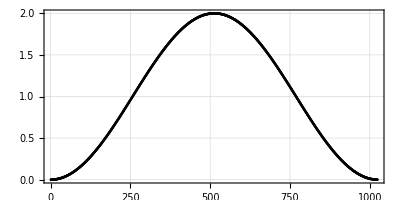
S$SAMPLING$RATE         :    1
S$COMPLEX$FLAG          :    False
S$RANGE                 :    0.5
S$WINDOW$ORDER          :    1
S$WINDOW$LENGTH         :    1024
S$INTERPOLATION$ORDER   :    8
S$INTERPOLATION$POINTS  :    12
S$FIT$LENGTH            :    1024
S$FIT$METHOD            :    Automatic
S$PROCESS               :    Function[Subtract[Slot[1], Mean[Slot[1]]]]

-Graphics-

```mathematica
(* Global basic variables and parameters can be printed by S$PRINT$VARIABLES[] or with option "Verbose" in S$SET$VARIABLES[] *)
S$PRINT$VARIABLES[]                 (* -- print global variables, parametes and plot window data *)
```

```mathematica
(* S$PROCESS[] function is not re-initialized by S$SET$VARIABLES[], but it can be changed manualy *)
(* This function is applied to the input signal before the application of window *)
(* Some examples of possible choices for S$PROCESS[] function: *)
(* Function[Subtract[Slot[1],Mean[Slot[1]]]]   -- subtract mean value *)
(* Function[Subtract[Slot[1],Median[Slot[1]]]] -- subtract median value *)
(* Standardize                                 -- standardize input signal *) 
(* Note: this function is applied to full input signal irrespective of selected window length *)
(* Filter can be added to S$PROCESS[] function, e.g.  Composition[...,Standardize] *)
(* Zeros (if used) should be padded after application of window function *)
S$PROCESS = Function[Subtract[Slot[1],Mean[Slot[1]]]]
```

#1-Mean[#1]&

```mathematica
(* Better S$PROCESS function can be defined using S$MEAN (not default) *)
S$PROCESS = Function[Subtract[Slot[1],S$MEAN[Slot[1]]]]
```

#1-S$MEAN[#1]&

```mathematica
(* Even better S$PROCESS function is S$WEIGHTED$MEAN (not default) *) 
S$PROCESS = Function[Subtract[Slot[1],S$WEIGHTED$MEAN[Slot[1]]]]
```

#1-S$WEIGHTED$MEAN[#1]&

## EXAMPLE-01: Frequency identification

```mathematica
(* In this example, basic frequency identification is performed for synthetic signals and some related functions are discussed  *)
```

```mathematica
(* Define test signals *)
(* Signal length *)
LEN = 4096 ;       
(* Main frequency *)                  
FRE = N[EulerGamma/E] ;
(* Test signal with one frequency *)
SG1 = Sin[2 Pi FRE Range[LEN]] ;    
(* Test signal with several frequencies (harmonics of the main frequency) *) 
SG2 = 1.0 Sin[2 Pi 1FRE Range[LEN]] + 0.1 Cos[2 Pi 2FRE Range[LEN]] + 0.01 Sin[2 Pi 3FRE Range[LEN]] + 0.001 Sin[2 Pi 4FRE Range[LEN]] ;
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* Re-initialization of basic variables and parameters *)
S$SET$VARIABLES[                     (* -- re-initiallization of basic variables and parameters *)
	1,                               (* -- signal sampling rate (integer) *)
	False,                           (* -- complex input signal flag (true or false) *)
	1,                               (* -- cosine window order (positive integer or real) *)
	1024,                            (* -- window length (integer) *)
	8,                               (* -- refined spectra interpolation order (integer) *)
	12,                              (* -- number of points to use in spectra interpolation (integer) *)
	1024,                            (* -- number of (randomly selected) points to use for signal fitting (integer) *)
	Automatic                        (* -- fitting method (valid method for ) LinearModelFit[], GeneralizedLinearModelFit[] or NonlinearModelFit[] *) 
] ;
S$PROCESS = Function[Subtract[Slot[1],Mean[Slot[1]]]] ;
(* Note that window length determines the number of data point used for frequency estimation *)
(* S$WINDOW$LENGTH points are taken for the given signal (starting from the head)*)
(* But S$PROCESS[] is applied to the full input signal *)
```

Normalized→False
FourierParameters→{-1,1}
Complex→False

{218}

{218,436,373,155}

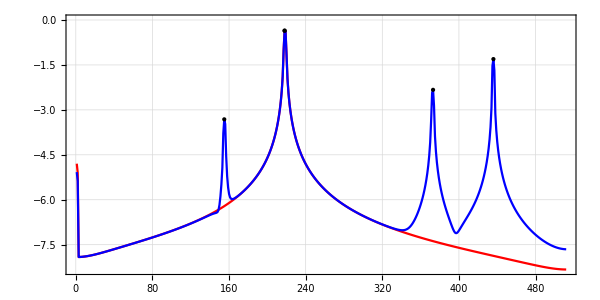

```mathematica
(* Function S$SPECTRA[] can be used to generate amplitude Fourier spectra (or use Periodogram[]) *) 
(* Possible options: *)
S$SPECTRA//Options//TableForm
(* Compute spectra of test signals *)
FS1 = S$SPECTRA[Times[Take[S$PROCESS[SG1],S$WINDOW$LENGTH],S$WINDOW$DATA]] ;
FS2 = S$SPECTRA[Times[Take[S$PROCESS[SG2],S$WINDOW$LENGTH],S$WINDOW$DATA]] ;
(* Spectra peaks can be obtained with S$FIND$PEAKS[] function (interface to FindPeaks[] function) *) 
(* S$FIND$PEAKS[<NUM>,<DAT>] attempts to find up to <NUM> (integer) peaks for given data <DAT> (list of reals) and returns peak positions sorted by the data values *)
(* Search for 1 peak in 1st spectra and for 4 peaks in 2nd spectra *)
PP1 = S$FIND$PEAKS[1,FS1] 
PP2 = S$FIND$PEAKS[4,FS2]
(* Get peaks data *) 
PP1 = Point[Transpose[List[PP1,Part[FS1,PP1]]]] ;
PP2 = Point[Transpose[List[PP2,Part[FS2,PP2]]]] ;
(* Plot spectra and peak points *)
ListPlot[
	List[FS1,FS2],
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotTheme -> "Detailed",
	PlotStyle -> List[Red,Blue],
	Joined -> True,
	Epilog -> List[
		Black,
		PointSize[Large],
		PP1,
		PP2
	]
]
```

{218}

{218,436,373,155}

{218}

{218,436,373,155}

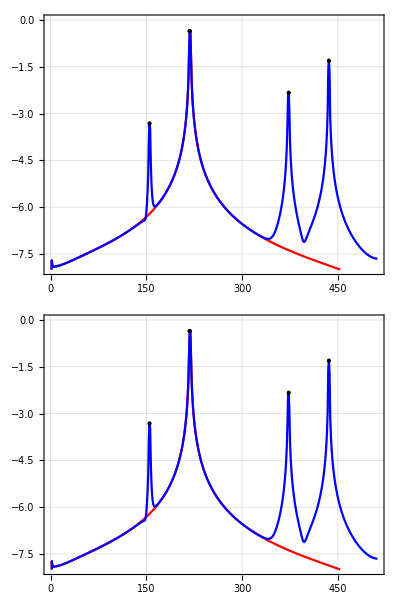

```mathematica
(* Effect at low frequencies can be reduced with S$MEAN or S$WEIGHTED$MEAN function *) 
S$PROCESS = Function[Subtract[Slot[1],S$MEAN[Slot[1],1]]] ;
FS1 = S$SPECTRA[Times[Take[S$PROCESS[SG1],S$WINDOW$LENGTH],S$WINDOW$DATA]] ;
FS2 = S$SPECTRA[Times[Take[S$PROCESS[SG2],S$WINDOW$LENGTH],S$WINDOW$DATA]] ;
PP1 = S$FIND$PEAKS[1,FS1] 
PP2 = S$FIND$PEAKS[4,FS2]
PP1 = Point[Transpose[List[PP1,Part[FS1,PP1]]]] ;
PP2 = Point[Transpose[List[PP2,Part[FS2,PP2]]]] ;
PL1 = ListPlot[List[FS1,FS2], PlotRange -> List[All,List[-8,0]], AspectRatio -> 1/2, ImageSize -> 600, PlotTheme -> "Detailed", PlotStyle -> List[Red,Blue], Joined -> True, Epilog -> List[Black,PointSize[Large],PP1,PP2]] ;
S$PROCESS = Function[Subtract[Slot[1],S$WEIGHTED$MEAN[Slot[1]]]] ;
FS1 = S$SPECTRA[Times[S$PROCESS[Take[SG1,S$WINDOW$LENGTH]],S$WINDOW$DATA]] ;
FS2 = S$SPECTRA[Times[S$PROCESS[Take[SG2,S$WINDOW$LENGTH]],S$WINDOW$DATA]] ;
PP1 = S$FIND$PEAKS[1,FS1] 
PP2 = S$FIND$PEAKS[4,FS2]
PP1 = Point[Transpose[List[PP1,Part[FS1,PP1]]]] ;
PP2 = Point[Transpose[List[PP2,Part[FS2,PP2]]]] ;
PL2 = ListPlot[List[FS1,FS2], PlotRange -> List[All,List[-8,0]], AspectRatio -> 1/2, ImageSize -> 600, PlotTheme -> "Detailed", PlotStyle -> List[Red,Blue], Joined -> True, Epilog -> List[Black,PointSize[Large],PP1,PP2]] ;
Grid[List[List[PL1],List[PL2]]]
(* Set to default *)
S$PROCESS = Function[Subtract[Slot[1],Mean[Slot[1]]]] ;
```

```mathematica
(* The main function for frequency identification is S$FREQUENCY[] *)
(* It uses procedure similar to Laskar's NAFF to estimate frequencies (see code for detailed implementation) *)
(* Function S$FREQUENCY[] has two forms: *)

(* <OUT> = S$FREQUENCY[<SIG>]                   -- estimate main (with largest Fourier amplitude) frequency for given input signal <SIG> *)
(* <SIG> -- input signal (list) *)
(* <OUT> = {<FRE>,<CAS>,<BIN>} *)
(* <FRE> -- freuency estiomation *)
(* <CAS> -- exit case *)
(* <BIN> -- corresponding maximum bin in spectra *)

(* <OUT> = S$FREQUENCY[<NUM>,<SIG>]             -- estimate <NUM>'th Fourier peak frequency for given input signal <SIG> *)
(* <NUM> -- peak number (integer) *)
(* <SIG> -- input signal (list) *)
(* <OUT> = {<FRE>,<CAS>,<BIN>} *)
(* <FRE> -- freuency estiomation *)
(* <CAS> -- exit case *)
(* <BIN> -- corresponding maximum bin in spectra *)

(* If approximation of several frequencies is required it might be better to use signal reconstruction to achieve better accuracy (see the corresponding example) *)
```

```mathematica
(* Estimate main frequency using the 1st form *)
(* Both variations of S$FREQUENCY[] return list with frequency estimation, execution case and bin position (see code source for description) *)
RS1 = S$FREQUENCY[SG1]
RS2 = S$FREQUENCY[SG2]
NumberForm[FRE,15]
NumberForm[First[RS1],15]
NumberForm[First[RS2],15]
(* Note that accuracy is better for the signal with one frequency due to the lack of aliasing *)
(* Usage of higher order windows, larger samples or higher frequency range reduces this effect *)
(* Signal reconstruction functions do not improve the accuracy of the first frequency *)
```

{0.212346,4,218}

{0.212346,4,218}

0.212345776239378

0.212345776235882

0.212345776236045

```mathematica
(* The second form can be used to estimate several frequencies at once *)
(* Since frequency range is [0,1/2], frequencies that are present in SG2 are seen as: *)
List[FRE,2FRE,3FRE,4FRE]
REF = Abs[Mod[List[FRE,2FRE,3FRE,4FRE],Times[2,S$RANGE],Times[Subtract[0,1],S$RANGE]]]
RES = Map[Composition[First,Curry[S$FREQUENCY][SG2]]][Range[4]]
Subtract[REF,RES]
```

{0.212346,0.424692,0.637037,0.849383}

{0.212346,0.424692,0.362963,0.150617}

{0.212346,0.424692,0.362963,0.150616}

{3.33314×10^-12,2.26367×10^-10,-1.83909×10^-8,1.16489×10^-6}

```mathematica
(* Accuracy vs window length *)
RES = Range[128,2048,128] ;
RES = Map[
	Function[
		Block[
			List[],
			S$SET$VARIABLES[1,False,1,Slot[1],8,12,1024,Automatic] ;
			List[Slot[1],Log10[Plus[$MachineEpsilon,Abs[Subtract[FRE,First[S$FREQUENCY[SG1]]]]]]]
		]
	],
	RES
] ;
RES//TableForm
```

128 | -8.15275
256 | -9.68834
384 | -9.57582
512 | -11.0305
640 | -10.8623
768 | -10.8156
896 | -12.5276
1024 | -11.4563
1152 | -11.6224
1280 | -12.9695
1408 | -11.8872
1536 | -12.3148
1664 | -13.2971
1792 | -12.2536
1920 | -13.0529
2048 | -13.0229

```mathematica
(* Accuracy vs window order *)
(* Note that for the case of several frequencies (or presents noise) large value of window order can lead to accuracy reduction *)
RES = Range[0,10,1] ;
RES = Map[
	Function[
		Block[
			List[],
			S$SET$VARIABLES[1,False,Slot[1],256,8,12,1024,Automatic] ;
			List[Slot[1],Log10[Plus[$MachineEpsilon,Abs[Subtract[FRE,First[S$FREQUENCY[SG1]]]]]]]
		]
	],
	RES
] ;
RES//TableForm
```

0 | -5.0681
1 | -9.68834
2 | -12.8328
3 | -15.3014
4 | -15.5153
5 | -15.6024
6 | -14.8665
7 | -14.7573
8 | -15.3014
9 | -15.4427
10 | -15.4427

```mathematica
(* For the case when sampling rate equals to one, frequency resolution for input real signal is [0,1/2] *)
(* Frequency resolution for complex signals is [0,1] *)
(* Re-initialization *)
(* Use compex signal *)
S$SET$VARIABLES[1,True,1,1024,8,12,1024,Automatic] ;
(* Define test signals (complex) *)
(* Signal length *)
LEN = 4096 ;
(* Main frequency *)                         
FRE = N[EulerGamma/E] ;
(* Test signal with one frequency *)
SG1 = Sin[2 Pi FRE Range[LEN]] + I Cos[2 Pi FRE Range[LEN]] ;    
(* Test signal with severeal frequencies (harmonics of the main frequency) *) 
SG2 = 1.0   (Sin[2 Pi 1FRE Range[LEN]] + I Cos[2 Pi 1FRE Range[LEN]]) + 
      0.1   (Cos[2 Pi 2FRE Range[LEN]] - I Sin[2 Pi 2FRE Range[LEN]]) + 
      0.01  (Sin[2 Pi 3FRE Range[LEN]] + I Cos[2 Pi 3FRE Range[LEN]]) +
      0.001 (Sin[2 Pi 4FRE Range[LEN]] + I Cos[2 Pi 4FRE Range[LEN]]) ;
```

{218}

{218,436,653,871}

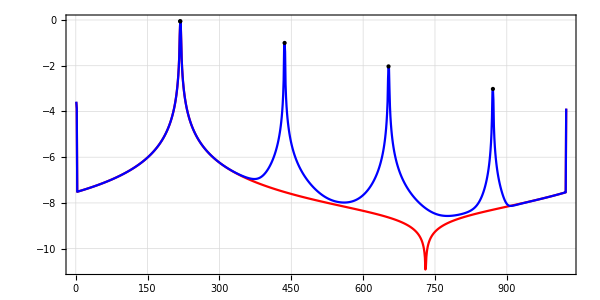

```mathematica
(* Compute spectra and peaks *)
FS1 = S$SPECTRA[Times[Take[S$PROCESS[SG1],S$WINDOW$LENGTH],S$WINDOW$DATA],Rule["Complex",True]] ;
FS2 = S$SPECTRA[Times[Take[S$PROCESS[SG2],S$WINDOW$LENGTH],S$WINDOW$DATA],Rule["Complex",True]] ;
PP1 = S$FIND$PEAKS[1,FS1] 
PP2 = S$FIND$PEAKS[4,FS2] 
PP1 = Point[Transpose[List[PP1,Part[FS1,PP1]]]] ;
PP2 = Point[Transpose[List[PP2,Part[FS2,PP2]]]] ;
(* Plot *)
ListPlot[
	List[FS1,FS2],
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotTheme -> "Detailed",
	PlotStyle -> List[Red,Blue],
	Joined -> True,
	Epilog -> List[
		Black,
		PointSize[Large],
		PP1,
		PP2
	]
]
```

```mathematica
(* Estimate main frequency using the 1st form (note improved accuracy in comparison with [0,1/2] range for both signals) *)
NumberForm[FRE,15]
NumberForm[First[RS1],15]
NumberForm[First[S$FREQUENCY[SG1]],15]
NumberForm[First[RS2],15]
NumberForm[First[S$FREQUENCY[SG2]],15]
```

0.212345776239378

0.212345776235882

0.212345776239381

0.212345776236045

0.212345776238824

```mathematica
(* Compute several frequencies *)
List[FRE,2FRE,3FRE,4FRE]
REF = Abs[Mod[List[FRE,2FRE,3FRE,4FRE],Times[2,S$RANGE],Times[Subtract[0,1],S$RANGE]]]
RES = Map[Composition[First,Curry[S$FREQUENCY][SG2]]][Range[4]]
Subtract[REF,RES]
```

{0.212346,0.424692,0.637037,0.849383}

{0.212346,0.424692,0.637037,0.849383}

{0.212346,0.424692,0.637037,0.849383}

{5.54223×10^-13,-5.26119×10^-11,-2.96482×10^-10,-1.69121×10^-9}

```mathematica
(* Another way to improve frequency resolution (and accuracy) is to use a larger sampling rate *)

(* SR = 1 *)
RAT = 1 ;
LEN = RAT 4096 ;
FRE = N[EulerGamma/E] ;
SIG = Sin[2 Pi FRE Range[LEN]/RAT]  ;
S$SET$VARIABLES[RAT,False,1,RAT 256,8,12,1024,Automatic] ;
S$RANGE
RES = S$FREQUENCY[SIG]
Subtract[FRE,First[RES]]

(* SR = 2 *)
RAT = 2 ;
LEN = RAT 4096 ;
FRE = N[EulerGamma/E] ;
SIG = Sin[2 Pi FRE Range[LEN]/RAT] + I Cos[2 Pi FRE Range[LEN]/RAT] ;
S$SET$VARIABLES[RAT,False,1,RAT 256,8,12,1024,Automatic] ;
S$RANGE
RES = S$FREQUENCY[SIG]
Subtract[FRE,First[RES]]
```

0.5

{0.212346,4,55}

2.04956×10^-10

1.

{0.212346,4,55}

-1.11386×10^-12

```mathematica
(* Prony's method can be used for frequency identification (and reconstruction) *)
(* For this method it's better to use small number of data points and even number of singular values to keep *)
LEN = 4096 ;
FRE = N[EulerGamma/E] ;
SIG = Sin[2 Pi FRE Range[LEN]]  ;

(* This function returns the list of singular values, exponents and signal model *)
List[SVL,EXP,MOD] = S$PRONY[  (* -- frequency estimation (reconstruction) with Prony's method  *)
	Take[SIG,128],            (* -- input signal *)
	2,                        (* -- number of singular values to keep (for a signal with one harmonic two singular values is sufficient) *)
	10.^-10                   (* -- real exponents cut off *)
] ;
NumberForm[FRE,15]
NumberForm[1/2 EXP//Im//Last,15]
MOD[s]
```

0.212345776239378

0.212345776239378

1. Sin[2.66842 s]

```mathematica
(* Prony's method for signal with several frequencies *)
LEN = 4096 ;
FRE = N[EulerGamma/E] ;
SIG = 1.0 Sin[2 Pi 1FRE Range[LEN]] + 0.1 Cos[2 Pi 2FRE Range[LEN]] + 0.01 Sin[2 Pi 3FRE Range[LEN]] + 0.001 Sin[2 Pi 4FRE Range[LEN]] ;
{SVL,EXP,MOD} = S$PRONY[
	Take[SIG,128],
	2*4,
	10.^-10
] ;
RES = Take[1/2EXP//Im,List[1,-1,2]]//Abs//Sort
REF = Abs[Mod[List[FRE,2FRE,3FRE,4FRE],Times[2,1/2],Times[Subtract[0,1],1/2]]]//Sort
Subtract[REF,RES]
MOD[s]
```

{0.150617,0.212346,0.362963,0.424692}

{0.150617,0.212346,0.362963,0.424692}

{1.69309×10^-15,1.38778×10^-16,-2.27596×10^-15,1.88738×10^-15}

0.1 Cos[5.33683 s]-0.001 Sin[1.89271 s]+1. Sin[2.66842 s]-0.01 Sin[4.56112 s]

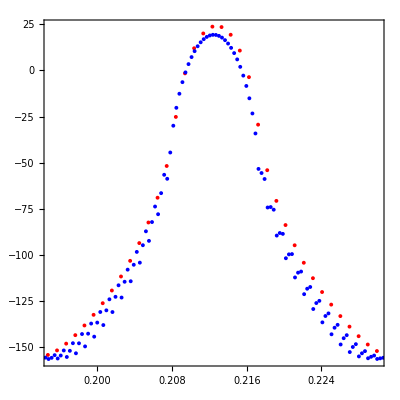

```mathematica
(* Padding zeros can be done with S$PAD$ZEROS[] function *) 
(* Zeros should be padded after application of window *)

S$SET$VARIABLES[RAT,False,4,1024,8,12,1024,Automatic] ;

LEN = 1024 ;
FRE = N[EulerGamma/E] ;
SIG = Sin[2 Pi FRE Range[LEN]]  ;

SG1 = Times[S$PROCESS[SIG],S$WINDOW$DATA] ;
(* Pad 512 zeros to both sides *)
SG2 = S$PAD$ZEROS[1024,1024,SG1] ;

Periodogram[
	List[SG1,SG2],
	Joined -> False,
	AspectRatio -> 1,
	Frame -> True,
	Axes -> False,
	PlotStyle -> List[Red,Blue],
	PlotRange -> List[List[0.195,0.23],All]
]
(* Signal with padded zeros has better frequency resolution and frequency can be estimating without peak refinement and interpolation is better *)
```

## EXAMPLE-02: Quasiperiodic decomposition

```mathematica
(* In this example, basic signal reconstruction is performed for synthetic signals and related functions are discussed *)
(* Signal reconstruction in most cases assumes quasiperiodic signals *)
(* But can be used for more general forms with dumping in some cases *)
(* Algorithms used for signal reconstruction are not identical with NAFF's procedure *)
(* In all cases, parameters of harmonics are obtained by fitting data for known set of frequencies or by Prony's method *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* The following functions for quasiperiodic decomposition of real signals are available: *)
(* S$QUASIPERIODIC$SUBTRACT[<ITR>,<TYP>,<SIG>]                        -- based on consecutive subtraction of the largest Fourier peak (with S$FREQUENCY[<SIG>]) *)
(* S$QUASIPERIODIC$PEAKS[<ITR>,<TYP>,<SIG>]                           -- reconstruction based on mutual identification of several peaks (with S$FREQUENCY[<NUM>,<SIG>]) *)
(* S$QUASIPERIODIC$HARMONICS$L1[<ORD>,<BAS>,<FAC>,<ERR>,<MET>,<SIG>]  -- reconstruction based on harmonic structure (signal has only harmonics of fundamental frequencies) using compressed sensing minimization *)
(* S$QUASIPERIODIC$HARMONICS$L2[<ORD>,<BAS>,<TYP>,<SIG>]              -- reconstruction based on harmonic structure (signal has only harmonics of fundamental frequencies) using quadratic minimization *)
(* S$PRONY[<SIG>,<NUM>,<TOL>]                                         -- reconstruction based on Prony's method *)
```

```mathematica
(* Re-initialization  *)
S$SET$VARIABLES[1,False,2,4096,8,12,1024,Automatic] ;
S$PROCESS
```

#1-Mean[#1]&

{0.212346,0.424692,0.362963,0.150617}

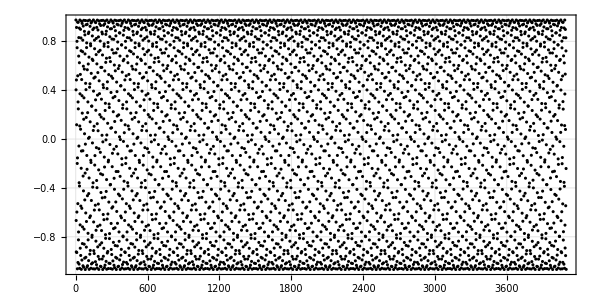

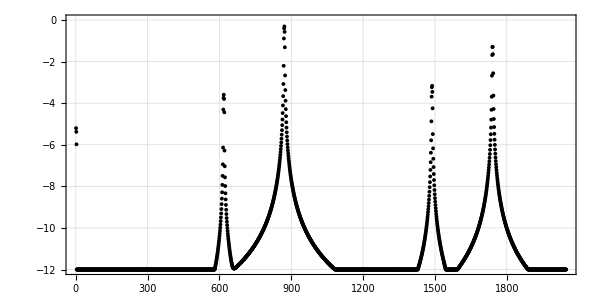

```mathematica
(* Define test (quasiperiodic) signal *)

(* Frequencies (main frequency and harmonics) *)
F1 = N[EulerGamma/E] ;
F2 = 2F1 ;
F3 = 3F1 ;
F4 = 4F1 ;
List[F1,F2,F3,F4] = Abs[Mod[List[F1,F2,F3,F4],Times[2,S$RANGE],Times[Subtract[0,1],S$RANGE]]]

(* Amplitudes *)
A1 = List[1.0,0.0]       ;
A2 = List[0.1,0.05]      ;
A3 = List[0.001,0.001]   ;
A4 = List[0.0001,0.0005] ;

SIG = A1.List[Sin[2 Pi F1 Range[S$WINDOW$LENGTH]],Cos[2 Pi F1 Range[S$WINDOW$LENGTH]]] +
	  A2.List[Sin[2 Pi F2 Range[S$WINDOW$LENGTH]],Cos[2 Pi F2 Range[S$WINDOW$LENGTH]]] +
	  A3.List[Sin[2 Pi F3 Range[S$WINDOW$LENGTH]],Cos[2 Pi F3 Range[S$WINDOW$LENGTH]]] +
	  A4.List[Sin[2 Pi F4 Range[S$WINDOW$LENGTH]],Cos[2 Pi F4 Range[S$WINDOW$LENGTH]]] ;
	  
(* Fourier amplitude spectra *)
SPE = S$SPECTRA[Times[S$WINDOW$DATA,S$PROCESS[SIG]]] ;
SPE = SPE /. X_ /; X ≤ -12. :> - 12. ;

(* Plot signal and spectra *)
(* Note the appearance of 'half-peak' for small frequencies caused by the combined effect of process and window function *)
(* In this example signal mean is zero, remove S$PROCESS to observe the effect on spectra *)
(* Also, try changing window order to observe the effect on spectra *)

ListPlot[
	SIG,
	AspectRatio -> 1/2,
	PlotTheme -> "Detailed",
	ImageSize -> 600,
	PlotStyle -> Black,
	ImagePadding -> 20,
	PlotRange -> All
]
ListPlot[
	SPE,
	AspectRatio -> 1/2,
	PlotTheme -> "Detailed",
	ImageSize -> 600,
	PlotStyle -> Black,
	ImagePadding -> 20,
	PlotRange -> All
]
```

```mathematica
(* S$QUASIPERIODIC$SUBTRACT *)
(* This function uses S$FREQUENCY[<SIG>] to estimate main frequency at each iteration *)
(* Use 5 iterations of consecutive largest Fourier peak subtraction *)
(* Note that the test signal has only 4 components, hence, the 5th component should be zero *)
SR1 = S$QUASIPERIODIC$SUBTRACT[   (* -- reconstruction based on consecutive subtraction of the largest Fourier peak *)
	5,                            (* -- number of iterations (integer), try to change this number and observe the result *)
	LinearModelFit,               (* -- minimization type (LinearModelFit, GeneralizedLinearModelFit or NonlinearModelFit) *)
	SIG                           (* -- input signal (list of reals) *)
] ;
(* S$QUASIPERIODIC$* functions return association with the following keys: *)
SR1["Information"]   (* -- contains minimization type, some parameters for the given type, execution case for S$FREQUENCY and flag showing monotonic behavior of amplitudes *)
SR1["Frequencies"]   (* -- list of frequencies for each component *)
SR1["Harmonics"]     (* -- estimated mean value and parameters *)
SR1["Function"]      (* -- model function *)
(* Compare estimated frequencies *)
Subtract[Most[SR1["Frequencies"]],List[F1,F2,F3,F4]]
```

{LinearModelFit,{{RSquared,1.},{AIC,-55018.2},{BIC,-54959.}},{4,4,4,4,4},True}

{0.212346,0.424692,0.362963,0.150617,0.212625}

{-1.36158×10^-14,{0.212346,{1.32737×10^-12,1.}},{0.424692,{0.05,0.1}},{0.362963,{0.001,0.001}},{0.150617,{0.0005,0.0001}},{0.212625,{8.13363×10^-14,-3.10195×10^-13}}}

-1.36158×10^-14+0.0005 Cos[0.946354 #1]+1.32737×10^-12 Cos[1.33421 #1]+8.13363×10^-14 Cos[1.33596 #1]+0.001 Cos[2.28056 #1]+0.05 Cos[2.66842 #1]+0.0001 Sin[0.946354 #1]+1. Sin[1.33421 #1]-3.10195×10^-13 Sin[1.33596 #1]+0.001 Sin[2.28056 #1]+0.1 Sin[2.66842 #1]&

{-1.11022×10^-16,-5.55112×10^-17,3.88578×10^-16,5.55112×10^-16}

```mathematica
(* S$QUASIPERIODIC$PEAKS *)
(* Use 5 peaks for reconstruction *)
SR2 = S$QUASIPERIODIC$PEAKS[      (* -- reconstruction based on mutual identification of several peaks *)
	5,                            (* -- number of peaks to use (integer) *)
	NonlinearModelFit,            (* -- minimization type *)
	SIG                           (* -- input signal *)
] ;
SR2["Information"]   (* -- contains minimization type, some parameters for a given type, execution case for S$FREQUENCY and flag showing monotonic behavior of amplitudes *)
SR2["Frequencies"]   (* -- list of frequencies for each component *)
SR2["Harmonics"]     (* -- estimated mean value and parameters *)
SR2["Function"]      (* -- model function *)
(* Compare estimated frequencies *)
Subtract[Most[SR2["Frequencies"]],List[F1,F2,F3,F4]]
```

{NonlinearModelFit,{{RSquared,1.},{AIC,-53688.},{BIC,-53628.8}},{4,4,4,4,4},True}

{0.212346,0.424692,0.362963,0.150617,0.285466}

{1.67688×10^-14,{0.212346,{1.32973×10^-12,1.}},{0.424692,{0.05,0.1}},{0.362963,{0.001,0.001}},{0.150617,{0.0005,0.0001}},{0.285466,{-1.90269×10^-14,2.43645×10^-14}}}

1.67688×10^-14+0.0005 Cos[0.946354 #1]+1.32973×10^-12 Cos[1.33421 #1]-1.90269×10^-14 Cos[1.79364 #1]+0.001 Cos[2.28056 #1]+0.05 Cos[2.66842 #1]+0.0001 Sin[0.946354 #1]+1. Sin[1.33421 #1]+2.43645×10^-14 Sin[1.79364 #1]+0.001 Sin[2.28056 #1]+0.1 Sin[2.66842 #1]&

{-1.11022×10^-16,2.77556×10^-16,-8.00471×10^-14,-1.72001×10^-13}

```mathematica
(* S$QUASIPERIODIC$HARMONICS$L1 *)
(* This function requires the list of known fundamental frequencies and uses the assumption of quasiperiodic structure *)
(* In our example only harmonics of fundamental frequencies are present and amplitudes of harmonic decrease *)
(* F1 is the fundamental frequency (if it's not known S$FREQUENCY can be used to estimate it (frequency with largest amplitude is assumed to be the fundamental frequency)) *)
FUN = First[S$FREQUENCY[SIG]] ;
SR3 = S$QUASIPERIODIC$HARMONICS$L1[
	20,                                  (* -- max order of harmonics, order of harmonic H = N_1 F_1 + N_2 F_2 + ... is defined as |N_1| + |N_2| + ... *)
	List[FUN],                           (* -- list of fundamental frequencies *)
	0.8,                                 (* -- factor (should be less or equal to one) *)
	10.^-10,                             (* -- error parameter for S$ORTHOGONAL$MATCHING$PURSUIT[] function  *)
	S$ORTHOGONAL$MATCHING$PURSUIT,       (* -- method, only S$ORTHOGONAL$MATCHING$PURSUIT is avalible *)
	SIG                                  (* -- signal *)
] ;

SR3["Information"]   (* -- total number of harmonics, method, number of harmonics/non-zero harmonics *)
SR3["Frequencies"]   (* -- list of frequencies for each component *)
SR3["Harmonics"]     (* -- estimated mean value and parameters *)
SR3["Function"]      (* -- model function *)
```

{20,S$ORTHOGONAL$MATCHING$PURSUIT,{20,4}}

{0.212346,0.424692,0.362963,0.150617}

{0.,{0.212346,{0.,1.}},{0.424692,{0.05,0.1}},{0.362963,{0.001,0.001}},{0.150617,{0.0005,0.0001}}}

Function[S$PAR,0.+0.0005 Cos[0.946354 S$PAR]+0.001 Cos[2.28056 S$PAR]+0.05 Cos[2.66842 S$PAR]+0.0001 Sin[0.946354 S$PAR]+1. Sin[1.33421 S$PAR]+0.001 Sin[2.28056 S$PAR]+0.1 Sin[2.66842 S$PAR]]

```mathematica
(* S$QUASIPERIODIC$HARMONICS$L2 is similar to S$QUASIPERIODIC$HARMONICS$L1 but uses quadratic minimization *)
FUN = First[S$FREQUENCY[SIG]] ;
SR4 = S$QUASIPERIODIC$HARMONICS$L2[
	20,                              (* -- max order of harmonics *)
	List[FUN],                       (* -- list of fundamental frequencies *)
	LinearModelFit,                  (* -- fit function *)
	SIG                              (* -- signal *)
] ;
(* Note that harmonics that do not present in the signal have small amplitudes *)
SR4["Harmonics"]
SR4["Harmonics"]//Chop//DeleteCases[List[_,List[0,0]]]
```

{-4.29049×10^-15,{0.212346,{1.34102×10^-12,1.}},{0.424692,{0.05,0.1}},{0.362963,{0.001,0.001}},{0.150617,{0.0005,0.0001}},{0.0617289,{1.7046×10^-14,-2.07928×10^-14}},{0.274075,{-3.61941×10^-14,-5.98041×10^-15}},{0.48642,{1.14854×10^-14,-4.44063×10^-15}},{0.301234,{-8.22035×10^-15,-2.08857×10^-15}},{0.088888,{5.66541×10^-15,-4.38919×10^-15}},{0.123458,{1.19066×10^-14,-1.42517×10^-15}},{0.335804,{2.32195×10^-15,5.29591×10^-15}},{0.451851,{1.76301×10^-14,-1.519×10^-14}},{0.239505,{-1.27258×10^-14,-6.35246×10^-15}},{0.0271591,{2.33274×10^-14,7.81487×10^-15}},{0.185187,{6.29069×10^-15,-1.63111×10^-14}},{0.397532,{-1.16272×10^-14,-5.1004×10^-14}},{0.390122,{-1.81475×10^-14,1.66029×10^-14}},{0.177776,{-1.61267×10^-14,3.47021×10^-14}},{0.0345697,{-3.44412×10^-14,-2.63957×10^-14}},{0.246916,{-4.99754×10^-15,2.19725×10^-15}}}

{0,{0.212346,{0,1.}},{0.424692,{0.05,0.1}},{0.362963,{0.001,0.001}},{0.150617,{0.0005,0.0001}}}

```mathematica
(* Function S$PRONY[] *)
SR5 = S$PRONY[
	Take[SIG,500],   (* -- input signal *)
	2*4,             (* -- number of singular values to keep *)
	10.^-6           (* -- cut-off for real part of exponents *)
] ;
Last[SR5][t]
```

0.0005 Cos[0.946354 t]+0.001 Cos[2.28056 t]+0.05 Cos[2.66842 t]+0.0001 Sin[0.946354 t]+1. Sin[1.33421 t]+0.001 Sin[2.28056 t]+0.1 Sin[2.66842 t]

```mathematica
(* Function S$NAFF[] *)
(* Implementation of Laskar's NAFF (without orthogonalization and computation of frequency by S$FREQUENCY[1,<...>]) *)
(* <OUT> = S$NAFF[<NUM>,<SIG>,<LEV>] *)
(* <OUT> = {{<FRE_1>,<COM_1>},...} *)
(* <FRE_I> -- component frequency *)
(* <COM_I> -- component (function of time S$PAR) *)
SR6 = S$NAFF[    
	4,               (* -- # of components to search (integer) *)
	SIG,             (* -- input signal (real or comlex list with length equal to S$WINDOW$LENGTH) *)
	10.^-10          (* -- chop level (real) *)
] 
Subtract[Map[First,SR6],List[F1,F2,F3,F4]]
```

{{0.212346,Function[S$PAR,1. Sin[1.33421 S$PAR]]},{0.424692,Function[S$PAR,0.05 Cos[2.66842 S$PAR]+0.1 Sin[2.66842 S$PAR]]},{0.362963,Function[S$PAR,0.001 Cos[2.28056 S$PAR]+0.001 Sin[2.28056 S$PAR]]},{0.150617,Function[S$PAR,0.0005 Cos[0.946354 S$PAR]+0.0001 Sin[0.946354 S$PAR]]}}

{-1.11022×10^-16,2.22045×10^-16,-6.55032×10^-15,8.9373×10^-15}

#1-Mean[#1]&

{0.212346,0.424692,0.362963,0.150617}

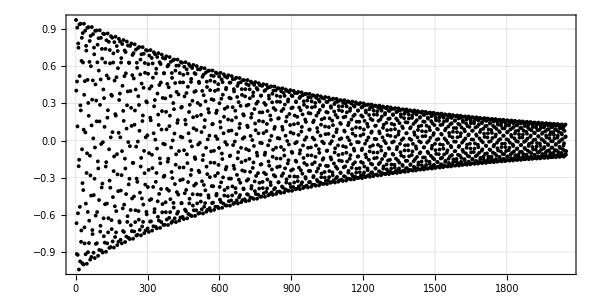

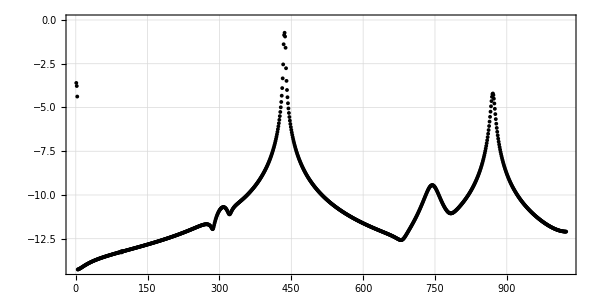

```mathematica
(* S$PRONY can be used for signals of the form: Exp[-a_i t](c_i Cos[2 Pi f_i t] + s_i Sin[2 Pi f_i t]) *)
(* S$QUASIPERIODIC$* functions can't be used for this form directry, but their low level components can *)
S$SET$VARIABLES[1,False,2,2048,8,12,2048,Automatic] ;
S$PROCESS

(* Define test  signal *)

(* Frequencies *)
F1 = N[EulerGamma/E] ;
F2 = 2F1 ;
F3 = 3F1 ;
F4 = 4F1 ;
List[F1,F2,F3,F4] = Abs[Mod[List[F1,F2,F3,F4],Times[2,S$RANGE],Times[Subtract[0,1],S$RANGE]]]

(* Amplitudes *)
A1 = List[1.0,0.0]       ;
A2 = List[0.1,0.05]      ;
A3 = List[0.001,0.001]   ;
A4 = List[0.0001,0.0005] ;

(* Exponents *)
E1 = - 0.001 ;
E2 = - 0.01 ;
E3 = - 0.05 ;
E4 = - 0.08 ;

SIG = Exp[E1 Range[S$WINDOW$LENGTH]] A1.List[Sin[2 Pi F1 Range[S$WINDOW$LENGTH]],Cos[2 Pi F1 Range[S$WINDOW$LENGTH]]] +
	  Exp[E2 Range[S$WINDOW$LENGTH]] A2.List[Sin[2 Pi F2 Range[S$WINDOW$LENGTH]],Cos[2 Pi F2 Range[S$WINDOW$LENGTH]]] +
	  Exp[E3 Range[S$WINDOW$LENGTH]] A3.List[Sin[2 Pi F3 Range[S$WINDOW$LENGTH]],Cos[2 Pi F3 Range[S$WINDOW$LENGTH]]] +
	  Exp[E4 Range[S$WINDOW$LENGTH]] A4.List[Sin[2 Pi F4 Range[S$WINDOW$LENGTH]],Cos[2 Pi F4 Range[S$WINDOW$LENGTH]]] ;
	  
(* Fourier amplitude spectra *)
SPE = S$SPECTRA[Times[S$WINDOW$DATA,S$PROCESS[SIG]]] ;

(* Plot signal and spectra *)
ListPlot[
	SIG,
	AspectRatio -> 1/2,
	PlotTheme -> "Detailed",
	ImageSize -> 600,
	PlotStyle -> Black,
	ImagePadding -> 20,
	PlotRange -> All
]
ListPlot[
	SPE,
	AspectRatio -> 1/2,
	PlotTheme -> "Detailed",
	ImageSize -> 600,
	PlotStyle -> Black,
	ImagePadding -> 20,
	PlotRange -> All
]
```

```mathematica
(* Prony's method with dumping *)
RS1 = Last[S$PRONY[Take[SIG,500],2*4,10.^-6]][t]
```

ⅇ^(-0.08 t) (0.0005 Cos[0.946354 t]+0.0001 Sin[0.946354 t])+1. ⅇ^(-0.001 t) Sin[1.33421 t]+ⅇ^(-0.05 t) (0.001 Cos[2.28056 t]+0.001 Sin[2.28056 t])+ⅇ^(-0.01 t) (0.05 Cos[2.66842 t]+0.1 Sin[2.66842 t])

```mathematica
List[F1,F2,F3,F4]
(* Find frequencies *)
FRE = Map[Composition[First,Curry[S$FREQUENCY][SIG]],Range[4]]
(* Fit data for known frequencies *)
MOD = S$FIT$MODEL[
	FRE,
	SIG,
	Rule["Type",NonlinearModelFit],
	Rule["Damping",True]
] ;
RS2 = Last[MOD][t]
```

{0.212346,0.424692,0.362963,0.150617}

{0.212346,0.424692,0.362936,0.150108}

5.70941×10^-9+ⅇ^(-0.0804957 t) (0.000504923 Cos[0.943154 t]+0.0000899674 Sin[0.943154 t])+ⅇ^(-0.001 t) (-3.42439×10^-8 Cos[1.33421 t]+1. Sin[1.33421 t])+ⅇ^(-0.0499815 t) (0.00100124 Cos[2.2804 t]+0.000997972 Sin[2.2804 t])+ⅇ^(-0.00999998 t) (0.0499998 Cos[2.66842 t]+0.0999999 Sin[2.66842 t])

```mathematica
(* Iterative procedure is not available for such signals from the get-go and accuracy for several frequencies can be low *)
```

```mathematica
(* Iretative procedure (just rewrite with loop if needed), but it can easily fail *)
FRE = List[] ;
DAT = SIG ;

(* 1st iteration *)
FRE = AppendTo[FRE,First[S$FREQUENCY[DAT]]] 
MOD = S$FIT$MODEL[FRE,SIG,Rule["Type",NonlinearModelFit],Rule["Damping",True]] ;
DAT = Last[MOD]["FitResiduals"] ;

(* 2nd iteration *)
FRE = AppendTo[FRE,First[S$FREQUENCY[DAT]]] 
MOD = S$FIT$MODEL[FRE,SIG,Rule["Type",NonlinearModelFit],Rule["Damping",True]] ;
DAT = Last[MOD]["FitResiduals"] ;

Last[MOD][t]

(* Here 3rd iteration will be wrong, look at main peak frequency *)
First[S$FREQUENCY[DAT]]
(* But 'correct' peak *)
First[S$FREQUENCY[3,DAT]]

(* 3nd iteration *)
FRE = AppendTo[FRE,First[S$FREQUENCY[3,DAT]]] 
MOD = S$FIT$MODEL[FRE,SIG,Rule["Type",NonlinearModelFit],Rule["Damping",True]] ;
DAT = Last[MOD]["FitResiduals"] ;

(* 4th iteration *)
FRE = AppendTo[FRE,First[S$FREQUENCY[4,DAT]]] 
MOD = S$FIT$MODEL[FRE,SIG,Rule["Type",NonlinearModelFit],Rule["Damping",True]] ;
DAT = Last[MOD]["FitResiduals"] ;

RS3 = Last[MOD][t] ;
```

{0.212346}

{0.212346,0.424692}

-1.99832×10^-7+ⅇ^(-0.001 t) (-1.26721×10^-6 Cos[1.33421 t]+1. Sin[1.33421 t])+ⅇ^(-0.0100011 t) (0.0499179 Cos[2.66842 t]+0.100051 Sin[2.66842 t])

0.212183

0.362963

{0.212346,0.424692,0.362963}

{0.212346,0.424692,0.362963,0.150616}

```mathematica
(* Iterative procedure (with peak subtraction) gives better accuracy but should be used with care *)
RS1
RS2
RS3
```

ⅇ^(-0.08 t) (0.0005 Cos[0.946354 t]+0.0001 Sin[0.946354 t])+1. ⅇ^(-0.001 t) Sin[1.33421 t]+ⅇ^(-0.05 t) (0.001 Cos[2.28056 t]+0.001 Sin[2.28056 t])+ⅇ^(-0.01 t) (0.05 Cos[2.66842 t]+0.1 Sin[2.66842 t])

5.70941×10^-9+ⅇ^(-0.0804957 t) (0.000504923 Cos[0.943154 t]+0.0000899674 Sin[0.943154 t])+ⅇ^(-0.001 t) (-3.42439×10^-8 Cos[1.33421 t]+1. Sin[1.33421 t])+ⅇ^(-0.0499815 t) (0.00100124 Cos[2.2804 t]+0.000997972 Sin[2.2804 t])+ⅇ^(-0.00999998 t) (0.0499998 Cos[2.66842 t]+0.0999999 Sin[2.66842 t])

4.31039×10^-12+ⅇ^(-0.0799999 t) (0.000500002 Cos[0.94635 t]+0.0000999871 Sin[0.94635 t])+ⅇ^(-0.001 t) (-6.56003×10^-11 Cos[1.33421 t]+1. Sin[1.33421 t])+ⅇ^(-0.0499999 t) (0.000999994 Cos[2.28056 t]+0.001 Sin[2.28056 t])+ⅇ^(-0.01 t) (0.05 Cos[2.66842 t]+0.1 Sin[2.66842 t])

## EXAMPLE-03: Quasiperiodic decomposition and FMA functions (symplectic map)

```mathematica
(* In this example, basic signal reconstruction is performed for the signal generated by iteration of quadratic symplectic map *)
(* Several initial conditions are used to produce both regular and chaotic orbits *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* Define quadratic symplectic map (Henon) *)
(* Linear frequencies and parameters *)
F1 = 2 Pi 0.38 ;
F2 = 2 Pi 0.41 ;
A1 = 0.0 ;
B1 = 1.0 ;
A2 = 0.0 ;
B2 = 1.0 ;
ClearAll[MAP] ;
MAP = With[
	{$Q1 = F1, $Q2 = F2, $W  = 1.0, $A1 = A1, $B1 = B1, $A2 = A2, $B2 = B2},
	Compile[
		{{X,_Real,1}},
		Block[
			{Q1,P1,Q2,P2},
			{Q1,P1,Q2,P2} = X ;
			{
				(Cos[$Q1] + $A1 Sin[$Q1])Q1 + ($W(Q1^2-Q2^2)+P1) $B1 Sin[$Q1], 
				(Cos[$Q1] - $A1 Sin[$Q1])($W(Q1^2-Q2^2)+P1) - Q1 (1 + $A1^2)/$B1 Sin[$Q1], 
				(Cos[$Q2] + $A2 Sin[$Q2])Q2 + ($W(-2 Q1 Q2) + P2) $B2 Sin[$Q2], 
				(Cos[$Q2] - $A2 Sin[$Q2])($W(-2 Q1 Q2) + P2) - (1 + $A2^2)/$B2 Q2 Sin[$Q2]
			}
		],
		CompilationOptions -> List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
```

```mathematica
(* Re-initialization  *)
S$SET$VARIABLES[1,False,4,8192,8,12,1024,Automatic] ;
```

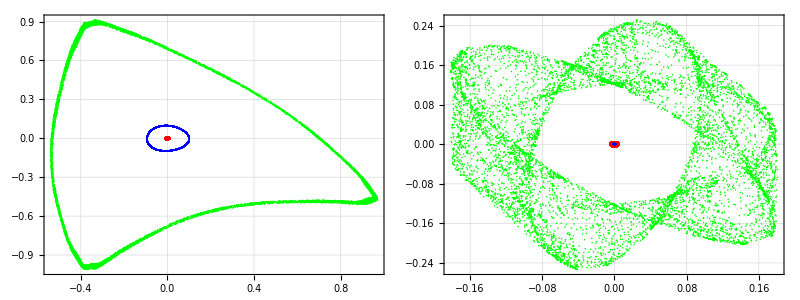

```mathematica
(* Define several trajectories *)
(* Compute orbits *)
TRJ1 = NestList[MAP,List[0.01,0.,0.005,0.0],S$WINDOW$LENGTH-1] ;        (* -- red   (regular) *)
TRJ2 = NestList[MAP,List[0.1,0.,0.001,0.0],S$WINDOW$LENGTH-1] ;         (* -- blue  (regular) *)
TRJ3 = NestList[MAP,List[0.7,0.,0.1,0.0],S$WINDOW$LENGTH-1] ;           (* -- green (chaotic) *)
(* Plot orbits *)
Grid[
	List[
		List[
			ListPlot[
				List[Part[TRJ1,All,List[1,2]],Part[TRJ2,All,List[1,2]],Part[TRJ3,All,List[1,2]]],
				AspectRatio->1,
				PlotTheme->"Detailed",
				ImageSize->400,
				PlotStyle->List[Red,Blue,Green],
				PlotRange->All
			],
			ListPlot[
				List[Part[TRJ1,All,List[3,4]],Part[TRJ2,All,List[3,4]],Part[TRJ3,All,List[3,4]]],
				AspectRatio->1,
				PlotTheme->"Detailed",
				ImageSize->400,
				PlotStyle->List[Red,Blue,Green],
				PlotRange->All
			]			
		]
	]
]
```

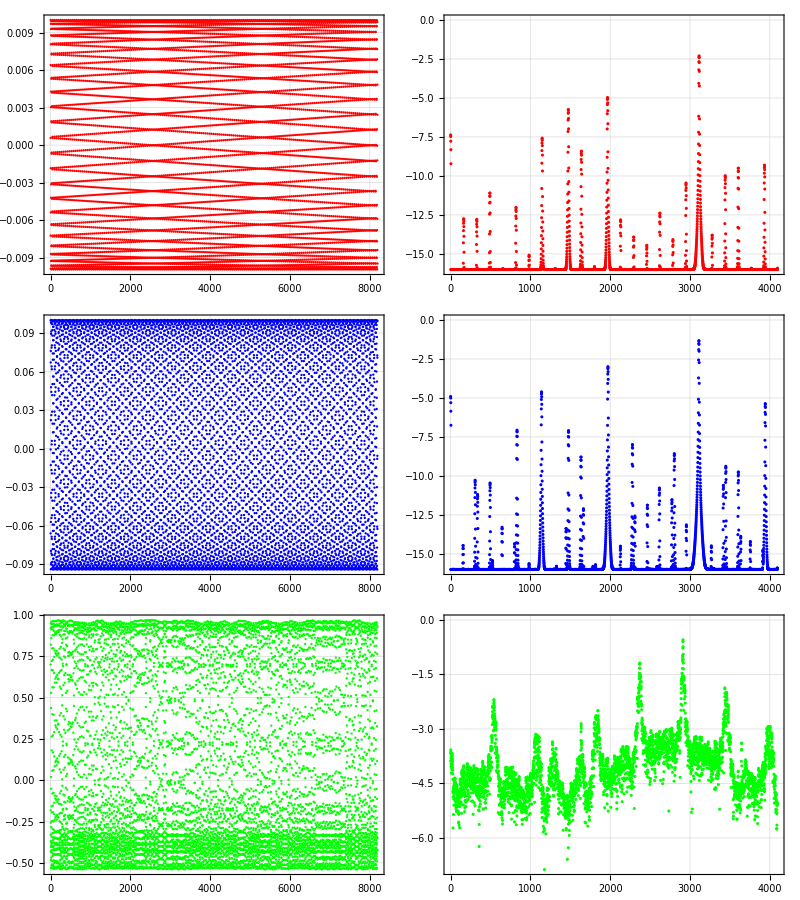

```mathematica
(* Define signals and plot spectra *)
(* In this example trajectories 1 and 2 are regular (red and blue) and trajectory 3 is chaotic (green), it has continuous spectra *)

(* Use evolution 1st coordinate as signal *)
SIG1 = First[Transpose[TRJ1]] ;
SIG2 = First[Transpose[TRJ2]] ;
SIG3 = First[Transpose[TRJ3]] ;

(* Compute spectra *)
SPE1 = S$SPECTRA[Times[S$WINDOW$DATA,S$PROCESS[SIG1]]] ;
SPE2 = S$SPECTRA[Times[S$WINDOW$DATA,S$PROCESS[SIG2]]] ;
SPE3 = S$SPECTRA[Times[S$WINDOW$DATA,S$PROCESS[SIG3]]] ;

(* Plot signals and corresponding spectra *)
Grid[
	List[
		List[
			ListPlot[SIG1,AspectRatio -> 1/2,PlotTheme -> "Detailed",ImageSize -> 600,PlotStyle -> Red,ImagePadding -> 40,PlotRange -> All],
			ListPlot[SPE1,AspectRatio -> 1/2,PlotTheme -> "Detailed",ImageSize -> 600,PlotStyle -> Red,ImagePadding -> 40,PlotRange -> All]
		],
		List[
			ListPlot[SIG2,AspectRatio -> 1/2,PlotTheme -> "Detailed",ImageSize -> 600,PlotStyle -> Blue,ImagePadding -> 40,PlotRange -> All],
			ListPlot[SPE2,AspectRatio -> 1/2,PlotTheme -> "Detailed",ImageSize -> 600,PlotStyle -> Blue,ImagePadding -> 40,PlotRange -> All]
		],
		List[
			ListPlot[SIG3,AspectRatio -> 1/2,PlotTheme -> "Detailed",ImageSize -> 600,PlotStyle -> Green,ImagePadding -> 40,PlotRange -> All],
			ListPlot[SPE3,AspectRatio -> 1/2,PlotTheme -> "Detailed",ImageSize -> 600,PlotStyle -> Green,ImagePadding -> 40,PlotRange -> All]
		]
	]
]
```

```mathematica
(* Chaotic trajectory is not quasiperiodic and it has no fundamental frequencies (it's not on a tori) *)
(* But for given signal one can find some 'frequency' approximation (see Laskar's papers) *)
(* Chaos indicator can be built on this idea if one compares this approximation for different window positions (FMA) *)

(* Compare mean frequency estimation on the first 4096 points and last 4096 points *)
S$SET$VARIABLES[1,False,4,4096,8,12,1024,Automatic] ;

Subtract[First[S$FREQUENCY[Take[SIG1,4096]]],First[S$FREQUENCY[Drop[SIG1,4096]]]]
Subtract[First[S$FREQUENCY[Take[SIG2,4096]]],First[S$FREQUENCY[Drop[SIG2,4096]]]]
Subtract[First[S$FREQUENCY[Take[SIG3,4096]]],First[S$FREQUENCY[Drop[SIG3,4096]]]]
(* One can see that deviation/difference in 'frequency' for chaotic orbit is larger *)

(* This can be done with S$FMA function (more details below and in FMA example) *)
S$FMA[List[SIG1]]
S$FMA[List[SIG2]]
S$FMA[List[SIG3]]
```

1.11022×10^-16

1.11022×10^-16

-0.000169672

{{{0.379996,0.379996}},{1.11022×10^-16},1.11022×10^-16}

{{{0.379688,0.379688}},{1.11022×10^-16},1.11022×10^-16}

{{{0.355158,0.355328}},{0.000169672},0.000169672}

```mathematica
(* Reconstruction of 2nd signal (blue) (reconstruction of 1st signal is similar and reconstruction of 3rd signal is meaningless) *)
(* Observe how info is changed for different number of iterations *)
S$QUASIPERIODIC$SUBTRACT[1,LinearModelFit,SIG2]["Information"]
S$QUASIPERIODIC$SUBTRACT[5,LinearModelFit,SIG2]["Information"]
S$QUASIPERIODIC$SUBTRACT[10,LinearModelFit,SIG2]["Information"]
S$QUASIPERIODIC$SUBTRACT[20,LinearModelFit,SIG2]["Information"]
```

{LinearModelFit,{{RSquared,0.999552},{AIC,-10489.6},{BIC,-10469.8}},{4},True}

{LinearModelFit,{{RSquared,1.},{AIC,-29798.9},{BIC,-29739.7}},{4,4,4,4,4},True}

{LinearModelFit,{{RSquared,1.},{AIC,-42074.4},{BIC,-41965.9}},{4,4,4,4,4,4,4,4,4,4},True}

{LinearModelFit,{{RSquared,1.},{AIC,-57421.9},{BIC,-57214.8}},{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},True}

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,4,8192,8,12,1024,Automatic] ;

(* Reconctruction with S$QUASIPERIODIC$SUBTRACT[] *)
SR1 = S$QUASIPERIODIC$SUBTRACT[20,LinearModelFit,SIG2];
SR1["Information"]

(* Reconctruction with S$QUASIPERIODIC$HARMONICS$L1[] *)
(* In this example, there are two fundamental frequencies (one for each degree of freedom) *)
FR1 = S$FREQUENCY[Part[TRJ2,All,1]]//First
FR2 = S$FREQUENCY[Part[TRJ2,All,3]]//First
(* For S$QUASIPERIODIC$HARMONICS$L1 one can try to find order and factor that produce small number of components *)
SR2 = S$QUASIPERIODIC$HARMONICS$L1[15,List[FR1,FR2],0.1,10.^-12,S$ORTHOGONAL$MATCHING$PURSUIT,SIG2] ;
SR2["Information"]

(* Reconctruction with S$PRONY[] *)
SR3 = S$PRONY[Take[SIG2,512],2 10,10.^-10] ;
```

{LinearModelFit,{{RSquared,1.},{AIC,-57404.7},{BIC,-57197.5}},{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4},True}

0.379688

0.409854

{15,S$ORTHOGONAL$MATCHING$PURSUIT,{240,34}}

```mathematica
(* Compare maximum residuals for the above reconstruction cases *)
Max[Abs[Subtract[SR1["Function"][Range[S$WINDOW$LENGTH]],SIG2]]]
Max[Abs[Subtract[SR2["Function"][Range[S$WINDOW$LENGTH]],SIG2]]]
Max[Abs[Subtract[Chop[Last[SR3][Range[S$WINDOW$LENGTH]]],SIG2]]]
```

5.38306×10^-13

3.66699×10^-9

2.07448×10^-7

```mathematica
(* Identification of harmonics can be done with S$IDENTIFY[] function *)
HAR = S$IDENTIFY[         (* -- identify harmonics *)
	20,                   (* -- max order (integer) *)
	List[FR1,FR2],        (* -- basis (list of fundamental frequencies) *)
	SR1["Frequencies"]    (* -- list of frequencies to identify *)
] ;
TableForm[Cases[HAR,List[a__,List[b_,c_]] :>  List[a,b x + c y]]]
(* frequency/harmonic/difference/representation *)
```

0.379688 | 0.379688 | 0. | x
0.240624 | 0.240624 | 4.44089×10^-16 | 2 x
0.139064 | 0.139064 | 2.58127×10^-15 | 3 x
0.481247 | 0.481247 | 2.66454×10^-15 | 4 x
0.101559 | 0.101559 | 7.29944×10^-13 | 5 x
0.180291 | 0.180291 | 1.19238×10^-13 | 2 y
0.278129 | 0.278129 | 1.32272×10^-12 | 6 x
0.342183 | 0.342183 | 1.96319×10^-11 | 7 x
0.199397 | 0.199397 | 7.71827×10^-13 | x+2 y
0.420915 | 0.420915 | 1.65737×10^-11 | 2 x+2 y
0.440021 | 0.440021 | 3.00809×10^-12 | x-2 y
0.0375051 | 0.0375051 | 3.27345×10^-10 | 8 x
0.0603325 | 0.0603325 | 3.08189×10^-10 | 2 x-2 y
0.417193 | 0.417193 | 1.92006×10^-10 | 9 x
0.319356 | 0.319356 | 4.3502×10^-10 | 3 x-2 y
0.0412269 | 0.0412269 | 1.54232×10^-10 | 3 x+2 y
0.338461 | 0.338461 | 1.94852×10^-9 | 4 x+2 y
0.300956 | 0.300956 | 4.46146×10^-9 | 4 x-2 y
0.203119 | 0.203119 | 6.25292×10^-9 | 10 x
0.281851 | 0.281851 | 2.88913×10^-8 | 5 x+2 y

```mathematica
(* Harmonics for given basis can be generated with S$HARMONICS[] function *) 
S$HARMONICS[             (* -- generate harmonics *)
	2,                   (* -- max order *)
	List[FR1,FR2]        (* -- basis *)
]
```

<|{0,1}→0.409854,{1,0}→0.379688,{0,2}→0.180291,{1,-1}→0.0301662,{1,1}→0.210458,{2,0}→0.240624|>

```mathematica
(* Small interface to sddsnaff is avalible with S$SDDSNAFF[] function *) 
SR4 = S$SDDSNAFF[       (* -- sddsnaff *)
	2,                  (* -- # of frequencies to look for *)
	SIG2                (* -- input signal *)
]

Take[SR1["Frequencies"],2]
SR4//Last//Map[First]
Subtract[Take[SR1["Frequencies"],2],SR4//Last//Map[First]]
```

{0,{{0.379688,0.09713,2.331,0.000446887},{0.240624,0.00205306,1.62119,0.000675}}}

{0.379688,0.240624}

{0.379688,0.240624}

{-7.96901×10^-12,4.7462×10^-15}

```mathematica
(* FMA related functions *)
(* S$DEVIATION[] *)
(* S$FMA[] *)
(* S$SHIFT[] *)
(* S$FMA$SHIFT[] *)
```

```mathematica
(* S$DEVIATION[] *)
(* Re-initialization *)
S$SET$VARIABLES[1,False,4,4096,8,12,1024,Automatic] ;

(* S$DEVIATION[<SIG>]         -- deviation of frequency estimation for the main peak *)
(* S$DEVIATION[<NUM>,<SIG>]   -- deviation of frequency estimation for selected peak *)
(* This function returns estimation of frequency for first and last S$WINDOW$LENGTH points of the given signal *)

(* Main peak *)
S$DEVIATION[SIG1]
S$DEVIATION[SIG2]
S$DEVIATION[SIG3]

(* 1st peak *)
S$DEVIATION[1,SIG1]
S$DEVIATION[1,SIG2]
S$DEVIATION[1,SIG3]

(* 2nd peak *)
S$DEVIATION[2,SIG1]
S$DEVIATION[2,SIG2]
S$DEVIATION[2,SIG3]
```

{0.379996,0.379996}

{0.379688,0.379688}

{0.355158,0.355328}

{0.379996,0.379996}

{0.379688,0.379688}

{0.355158,0.355328}

{0.240007,0.240007}

{0.240624,0.240624}

{0.289149,0.289178}

```mathematica
(* S$FMA[] *)
(* Re-initialization *)
S$SET$VARIABLES[1,False,4,4096,8,12,1024,Automatic] ;

(* S$FMA[<SIG>]               -- deviation of frequency estimation for the main peak (the difference is computed) for a list of signals  *)
(* S$FMA[<NUM>,<SIG>]         -- deviation of frequency estimation for selected peak *)

(* {{{f_1_1,f_1_2},{f_2_1,f_2_2}},{d_1,d_2},d} *)
(* f_1_1 -- frequency estimation for 1st signal on first interval (main frequency) *)
(* f_1_2 -- frequency estimation for 1st signal on last interval (main frequency) *)
(* f_2_1 -- frequency estimation for 2nd signal on first interval (main frequency) *)
(* f_2_2 -- frequency estimation for 2nd signal on last interval (main frequency) *)
(* d_1 = f_1_1 - f_1_2 // Abs *)
(* d_2 = f_2_1 - f_2_2 // Abs *)
(* d = Norm[{d1,d2}]) *)
S$FMA[Transpose[Part[TRJ1,All,List[1,3]]]]
S$FMA[Transpose[Part[TRJ2,All,List[1,3]]]]
S$FMA[Transpose[Part[TRJ3,All,List[1,3]]]]

(* {{{{f_1_1_1,f_1_1_2},{f_1_2_1,f_1_2_2}},{{f_2_1_1,f_2_1_2},{f_2_2_1,f_2_2_2}}},{{d_1_1,d_1_2},{d_2_1,d_2_2}},{d_1,d_2}} *)
(* f_1_1_1 -- 1st signal 1st peak 1st interval *)
(* f_1_1_2 -- 1st signal 1st peak lst interval *)
(* f_1_2_1 -- 1st signal 2nd peak 1st interval *)
(* f_1_2_2 -- 1st signal 2nd peak lst interval *)
(* f_2_1_1 -- 2nd signal 1st peak 1st interval *)
(* f_2_1_2 -- 2nd signal 1st peak lst interval *)
(* f_2_2_1 -- 2nd signal 2nd peak 1st interval *)
(* f_2_2_2 -- 2nd signal 2nd peak lst interval *)
(* d_1_1 = f_1_1_1 - f_1_1_2 // Abs *)
(* d_1_2 = f_1_2_1 - f_1_2_2 // Abs*)
(* d_2_1 = f_2_1_1 - f_2_1_2 // Abs*)
(* d_2_2 = f_2_2_1 - f_2_2_2 // Abs*)
(* d_1 = Norm[{d_1_1,d_1_2}]*)
(* d_2 = Norm[{d_2_1,d_2_2}]*)
S$FMA[2,Transpose[Part[TRJ1,All,List[1,3]]]]
S$FMA[2,Transpose[Part[TRJ2,All,List[1,3]]]]
S$FMA[2,Transpose[Part[TRJ3,All,List[1,3]]]]
```

{{{0.379996,0.379996},{0.409998,0.409998}},{1.11022×10^-16,8.88178×10^-16},8.9509×10^-16}

{{{0.379688,0.379688},{0.409854,0.409854}},{5.55112×10^-17,3.88578×10^-16},3.92523×10^-16}

{{{0.355158,0.355328},{0.400114,0.400149}},{0.000169672,0.000034587},0.000173162}

{{{{0.379996,0.379996},{0.240007,0.240007}},{{0.409998,0.409998},{0.210006,0.210006}}},{{1.11022×10^-16,1.64591×10^-14},{8.88178×10^-16,3.66374×10^-15}},{1.64594×10^-14,3.76986×10^-15}}

{{{{0.379688,0.379688},{0.240624,0.240624}},{{0.409854,0.409854},{0.210458,0.210458}}},{{5.55112×10^-17,1.33227×10^-15},{3.88578×10^-16,1.22125×10^-15}},{1.33342×10^-15,1.28157×10^-15}}

{{{{0.355158,0.355328},{0.289149,0.289178}},{{0.400114,0.400149},{0.244709,0.244496}}},{{0.000169672,0.0000294279},{0.000034587,0.000212896}},{0.000172206,0.000215687}}

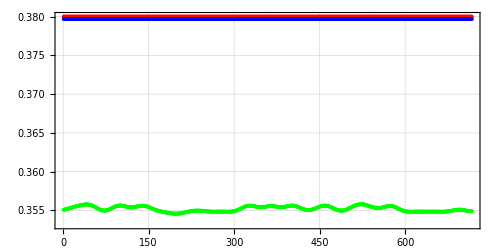

```mathematica
(* S$SHIFT[] *)
(* Re-initialization *)
S$SET$VARIABLES[1,False,4,1024,8,12,1024,Automatic] ;

(* S$SHIFT[<SHI>,<SIG>] -- compute frequency approximation with shifting window by <SHI> (integer) *)

(* Samples are generated by shifting window *) 
SHI1 = S$SHIFT[10,SIG1] ;
SHI2 = S$SHIFT[10,SIG2] ;
SHI3 = S$SHIFT[10,SIG3] ;

ListPlot[
	List[SHI1,SHI2,SHI3],
	AspectRatio->1/2,
	PlotTheme->"Detailed",
	ImageSize->500,
	PlotStyle->List[Red,Blue,Green]
]
```

```mathematica
(* S$FMA$SHIFT[] *)
(* {{{f_1_1,f_1_2,...},{f_2_1,f_2_2,...}},{d_1,d_2},d} *)
(* f_1_i -- estimation for 1st signal and ith sample *)
(* f_2_i -- estimation for 2nd signal and ith sample *)
(* d_1 = StandardDeviation[{f_1_1,...}] *)
(* d_2 = StandardDeviation[{f_2_1,...}] *)
(* d = Norm[{d1,d2}] *)
S$FMA$SHIFT[1024,Transpose[Part[TRJ1,All,List[1,3]]]]
S$FMA$SHIFT[1024,Transpose[Part[TRJ2,All,List[1,3]]]]
S$FMA$SHIFT[1024,Transpose[Part[TRJ3,All,List[1,3]]]]
```

{{{0.379996,0.379996,0.379996,0.379996,0.379996,0.379996,0.379996},{0.409998,0.409998,0.409998,0.409998,0.409998,0.409998,0.409998}},{6.28037×10^-16,6.67289×10^-16},9.16354×10^-16}

{{{0.379688,0.379688,0.379688,0.379688,0.379688,0.379688,0.379688},{0.409854,0.409854,0.409854,0.409854,0.409854,0.409854,0.409854}},{1.79877×10^-16,5.79996×10^-16},6.07249×10^-16}

{{{0.355079,0.355609,0.354624,0.355116,0.355492,0.355657,0.354836},{0.400061,0.400258,0.39995,0.400102,0.40022,0.400255,0.399994}},{0.000397281,0.000126202},0.000416845}

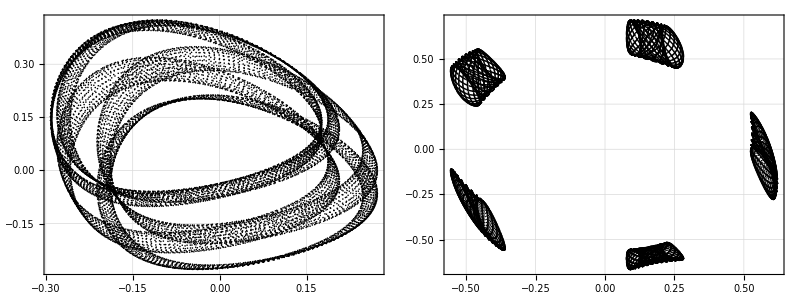

```mathematica
(* FMA for resonance trajectory *)
(* Generate resonance trajectory *)
TRJ = NestList[MAP,List[0.1106,0.,0.54,0.0],2^14-1] ; 
Grid[
	List[
		List[
			ListPlot[
				Part[TRJ,All,List[1,2]],
				AspectRatio->1,
				PlotTheme->"Detailed",
				ImageSize->400,
				PlotStyle->Black,
				PlotRange->All
			],
			ListPlot[
				Part[TRJ,All,List[3,4]],
				AspectRatio->1,
				PlotTheme->"Detailed",
				ImageSize->400,
				PlotStyle->Black,
				PlotRange->All
			]			
		]
	]
]
```

```mathematica
(* For resonance trajectories, FMA indicator might appear to be large *)
(* This is due to the modulation of frequency estimation *)
(* To remove this modulation larger samples should be used *)
(* Thus, for regular orbit deviation approaches zero with larger samples, this is not the case for chaotic orbits *)
S$SET$VARIABLES[1,False,2,1024,8,12,1024,Automatic]
S$FMA[Transpose[Part[TRJ,All,List[1,3]]]]
S$SET$VARIABLES[1,False,2,2 1024,8,12,1024,Automatic]
S$FMA[Transpose[Part[TRJ,All,List[1,3]]]]
S$SET$VARIABLES[1,False,2,4 1024,8,12,1024,Automatic]
S$FMA[Transpose[Part[TRJ,All,List[1,3]]]]
S$SET$VARIABLES[1,False,2,6 1024,8,12,1024,Automatic]
S$FMA[Transpose[Part[TRJ,All,List[1,3]]]]
S$SET$VARIABLES[1,False,2,8 1024,8,12,1024,Automatic]
S$FMA[Transpose[Part[TRJ,All,List[1,3]]]]
```

{{{0.372272,0.372387},{0.399928,0.400082}},{0.000114898,0.000154666},0.000192674}

{{{0.372336,0.372305},{0.400014,0.399973}},{0.0000309278,0.0000417086},0.0000519244}

{{{0.372325,0.372326},{0.399999,0.400001}},{9.7953×10^-7,1.32042×10^-6},1.64408×10^-6}

{{{0.372325,0.372326},{0.4,0.4}},{5.55202×10^-8,7.47476×10^-8},9.31112×10^-8}

{{{0.372326,0.372326},{0.4,0.4}},{5.87834×10^-9,7.93869×10^-9},9.87814×10^-9}

{{0.0000227402,0.0000306481},0.0000381631}

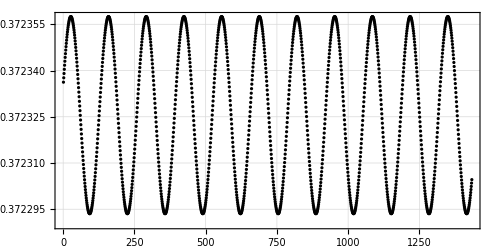

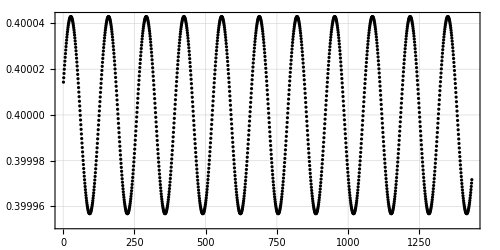

```mathematica
(* Frequency modulation *)
S$SET$VARIABLES[1,False,2,2048,8,12,1024,Automatic] ;
MOD = S$FMA$SHIFT[10,Transpose[Part[TRJ,All,List[1,3]]]] ;
MOD//Rest
(* Here modulation is regular, it's amplitude and period depend on the distance of initial condition with respect to separatrix *)
ListPlot[
	MOD//First//First,
	AspectRatio->1/2,
	PlotTheme->"Detailed",
	ImageSize->500,
	PlotStyle->Black
]
ListPlot[
	MOD//First//Last,
	AspectRatio->1/2,
	PlotTheme->"Detailed",
	ImageSize->500,
	PlotStyle->Black
]
```

```mathematica
(* Frequency footprint *)

REG = NestList[MAP,List[0.1106,0.,0.54,0.0],2^20-1] ;              (* -- regular trj *)
CHA = NestList[MAP,List[0.6892500005,0.,0.1,0.0],2^20-1] ;         (* -- chaotic trj *)

(* Compute FMA with shift *)
S$SET$VARIABLES[1,False,2,2048,8,12,1024,Automatic] ;

REG = S$FMA$SHIFT[50,Transpose[Part[REG,All,List[1,3]]]] ;
CHA = S$FMA$SHIFT[50,Transpose[Part[CHA,All,List[1,3]]]] ;

Last[REG]
Last[CHA]
```

0.0000379313

2.22287×10^-6

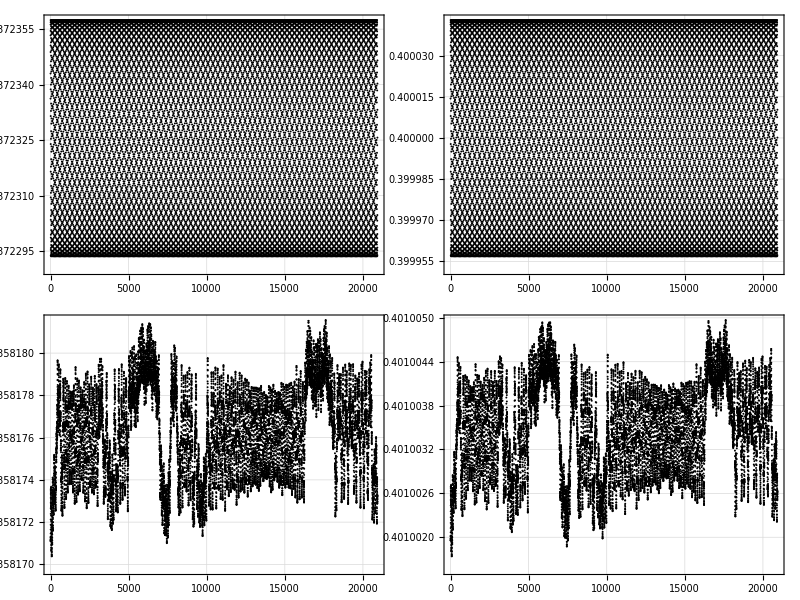

```mathematica
(* Plot results *)
Grid[
	List[
		List[
			ListPlot[REG//First//First,AspectRatio->1/2,PlotTheme->"Detailed",ImageSize->500,PlotStyle->Black,PlotRange->All],
			ListPlot[REG//First//Last,AspectRatio->1/2,PlotTheme->"Detailed",ImageSize->500,PlotStyle->Black,PlotRange->All]
		],
		List[
			ListPlot[CHA//First//First,AspectRatio->1/2,PlotTheme->"Detailed",ImageSize->500,PlotStyle->Black,PlotRange->All],
			ListPlot[CHA//First//Last,AspectRatio->1/2,PlotTheme->"Detailed",ImageSize->500,PlotStyle->Black,PlotRange->All]
		]
	]
]
```

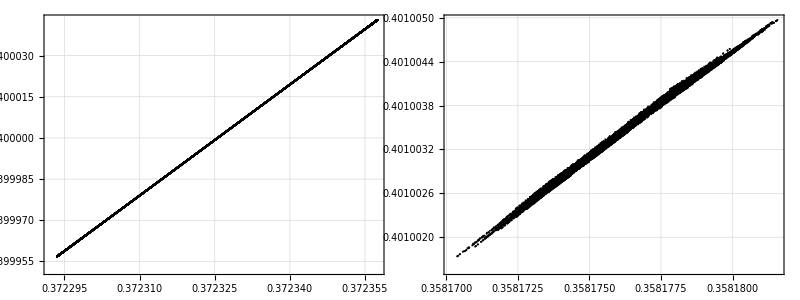

```mathematica
(* Plot results *)
Grid[
	List[
		List[
			ListPlot[Transpose[First[REG]],AspectRatio->1,PlotTheme->"Detailed",ImageSize->500,PlotStyle->Black,PlotRange->All],
			ListPlot[Transpose[First[CHA]],AspectRatio->1,PlotTheme->"Detailed",ImageSize->500,PlotStyle->Black,PlotRange->All]
		]
	]
]
```

```mathematica
(* From this example, it is clear that FMA indicator can produce suspicious results when used without proper care *)
(* Here indicator values are larger for regular trajectory when standard deviation is used *)
(* But from frequency dependence on window shift, the difference is clear  *) 
(* One can perform additional FMA to get correct result (but this procedure can be computationally expensive) *)
(* In most cases normal FMA is sufficient *)
(* Note that if the accuracy of frequency identification is high, the second pass is effectively performed on numerical noise  *)
(* To account for such case, one can add a small signal to list of frequencies before the second pass *)
S$SET$VARIABLES[1,False,2,4096,8,12,1024,Automatic] ;
S$FMA[First[REG]]
S$FMA[First[CHA]]
```

{{{0.0377955,0.0377955},{0.0377955,0.0377955}},{1.1751×10^-13,1.18745×10^-13},1.6706×10^-13}

{{{0.00900667,0.00764003},{0.00900662,0.00763858}},{0.00136664,0.00136804},0.00193371}

{3 x==1,3 y==1,x-2 y==0,x+2 y==1,2 x-y==0,2 x+y==1}

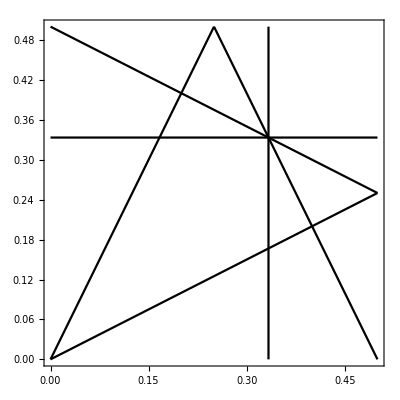

```mathematica
(* S$RESONANCE$LINES[] or S$RESONANCE$PLOT[] *)
(* This function can be used to generate resonance lines for 2 dof systems *)
(* Resonance line have the following form: *)
(* A X + B Y == C, with A, B and C being integers (an additional constraint is imposed on A, A>0) *)
(* Resonance order is |A| + |B| *)
LIN = S$RESONANCE$LINES[       (* -- generate resonance lines *)
	{x,y},                     (* -- symbols to use for frequencies *)
	3,                         (* -- resonance order *)
	0,                         (* -- horizontal frequency integer part *)
	{0,0.5},                   (* -- horizontal range *)
	0,                         (* -- verticle frequency integer part *) 
	{0,0.5}                    (* -- verticle range *)
]
ContourPlot[Evaluate[LIN],{x,0,0.5},{y,0,0.5},ContourStyle->Black]
```

## EXAMPLE-04: FMA

```mathematica
(* Frequency Map Analysis *)

(* In this example, basic FMA workflow is presented *)
(* FMA is based on accurate frequency computation for different parts of given signal *)
(* Here, FMA is performed for different sample length and shifted window *)
(* Example of FMA resolution refinement for frequency space is given together with some analysis of the results *)
```

```mathematica
(* For all cases, initial conditions are generated on a rectangular grid in space of coordinates for small fixed values of momenta *)

(* Case-1 *)
(*    2^11 iterations are performed for all initial conditions *)
(*    For initials that stay inside aperture for all iterations, FMA is performed with 2nd order window and sample size equal to 2^10 using complex data *)
(*    Frequencies are defined as mean values *)
(*    FMA indicator is defined as the norm of frequency deviations *)

(* Case-2 *)
(*    2^12 iterations are performed for all initial conditions *)
(*    For initials that stay inside aperture for all iterations, FMA is performed with 2nd order window and sample size equal to 2^11 using complex data *)
(*    Frequencies are defined as mean values *)
(*    FMA indicator is defined as the norm of frequency deviations *)

(* Case-3 *)
(*    2^16 iterations are performed for all initial conditions *)
(*    For initials that stay inside aperture for all iterations, FMA is performed with 2nd order window, sample size equal to 2^10 and window shift 40 using real data *)
(*    Frequencies are defined as mean values of corresponding frequency lists *)
(*    FMA indicator is defined by additional FMA for frequency lists with 2nd order window and sample size equal to 2^10 using real data *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* Define quadratic symplectic map with internal aperture (Henon) *)
(* Set map parameters *)
F1 = 2 Pi 0.38 ;
F2 = 2 Pi 0.41 ;
A1 = 0.0 ;
B1 = 1.0 ;
A2 = 0.0 ;
B2 = 1.0 ;
(* Generate compiled map *)
ClearAll[MAP] ;
MAP = With[
	{$Q1 = F1, $Q2 = F2, $W = 1.0, $A1 = A1, $B1 = B1, $A2 = A2, $B2 = B2},
	Compile[
		{{X,_Real,1}},
		Block[
			{W,Q1,P1,Q2,P2},
			{W,Q1,P1,Q2,P2} = X ;
			(* Check aperture and change flag *)
			If[
				Greater[Norm[List[Q1,Q2]],5.],
				W = 0. ;
			] ;
			(* Iterate for valid flag value *)
			If[
				W > 0.5,
				List[
					W,
					(Cos[$Q1] + $A1 Sin[$Q1])Q1 + ($W(Q1^2-Q2^2)+P1) $B1 Sin[$Q1], 
					(Cos[$Q1] - $A1 Sin[$Q1])($W(Q1^2-Q2^2)+P1) - Q1 (1 + $A1^2)/$B1 Sin[$Q1], 
					(Cos[$Q2] + $A2 Sin[$Q2])Q2 + ($W(-2 Q1 Q2) + P2) $B2 Sin[$Q2], 
					(Cos[$Q2] - $A2 Sin[$Q2])($W(-2 Q1 Q2) + P2) - (1 + $A2^2)/$B2 Q2 Sin[$Q2]
				],
				{W,Q1,P1,Q2,P2}
			]
		],
		CompilationOptions -> List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
```

```mathematica
(* Case-1 *)
(* Intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,1024,8,12,1024,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA,VAL,FRE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2048,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			FRE = Map[Mean,First[FMA]] ;
			VAL = Log10[Plus[$MachineEpsilon,Last[FMA]]] ;
			Flatten[List[Part[POI,List[2,4]],FRE,VAL]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["test_fma_data_1.mx",DAT,"MX"]
```

501

501

251001

{179.571,Null}

103707

0.413174

test_fma_data_1.mx

```mathematica
(* Case-2 *)
(* Intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,2048,8,12,1024,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA,VAL,FRE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[4096,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			FRE = Map[Mean,First[FMA]] ;
			VAL = Log10[Plus[$MachineEpsilon,Last[FMA]]] ;
			Flatten[List[Part[POI,List[2,4]],FRE,VAL]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["test_fma_data_2.mx",DAT,"MX"]
```

501

501

251001

{300.494,Null}

102708

0.409194

test_fma_data_2.mx

```mathematica
(* Case-3 *)
(* Intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,False,2,1024,8,12,1024,Automatic] ;
(* Task function *)
(* After FMA with window shift list of frequencies is generated *)
(* For this list additional FMA is performed *)
(* If for some initial condition accuracy of frequency is high, then additional FMA is applied to numerical noise *)
(* To aviod this, small signal is added to frequency list *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA,VAL,FRE,ADD},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2^16,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = First[S$FMA$SHIFT[40,Transpose[Part[DAT,All,List[2,4]]]]] ;
			FRE = Map[Mean,FMA] ;
			ADD = Times[N[Power[10,Times[Subtract[0,1],12]]],Sin[Times[2,Pi,Divide[EulerGamma,E],Range[Length[First[FMA]]]]]] ;
			FMA = Plus[FMA,ConstantArray[ADD,Plus[1,1]]] ;
			FMA = S$FMA[FMA] ;
			VAL = Log10[Plus[$MachineEpsilon,Last[FMA]]] ;
			Flatten[List[Part[POI,List[2,4]],FRE,VAL]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["test_fma_data_3.mx",DAT,"MX"]
```

501

501

251001

{119067.,Null}

99303

0.395628

test_fma_data_3.mx

```mathematica
(* Import FMA test data *)
SetDirectory[NotebookDirectory[]] ;
DAT1 = Import["test_fma_data_1.mx"] ;  (* -- case-1 FMA data *)
DAT2 = Import["test_fma_data_2.mx"] ;  (* -- case-2 FMA data *)
DAT3 = Import["test_fma_data_3.mx"] ;  (* -- case-3 FMA data *)
Length[DAT1]
Length[DAT2]
Length[DAT3]
```

103707

102708

99303

```mathematica
(* Use MaTeX for plot labels *)
(* https://github.com/szhorvat/MaTeX/releases *)
<< MaTeX` ;
```

```mathematica
(* Case-1 (results) *)
(* FMA results are usually presented as a color plot in space of coordinates and space of frequencies where color indicates FMA index value *)

(* FMA data in space of coordinates {{x_1,y_1,fma_1},{x_2,y_2,fma_2},...} *)
DAT = Part[DAT1,All,List[1,2,-1]] ;  
(* The first step is to set parameters *)
LEV = 0. ;                     (* -- FMA index level, this value will be used for initials that left the aperture *)
INT = List[-8.,-3.] ;          (* -- FMA index range, values outside of this range will be shifted to endpoints *)
HOR = List[-1.0,1.0] ;         (* -- horizontal interval *)
VER = List[0.0,1.0] ;          (* -- vertical interval *)
(* Binarize data *)
BIN = S$BINARIZE$REGION[
	500,                       (* -- number of bins to use for the horizontal plane *)
	500,                       (* -- number of bins to use for the vertical plane *)
	HOR,                       (* -- horizontal interval *)
	VER,                       (* -- vertical interval *)
	DAT,                       (* -- input data *)
	Rule["Level",LEV]          (* -- data default value *)
] ;

(* Binarized data can be plotted with S$COLOR$PLOT[] function *)
(* Some global variables used by this function can be changed *)
S$COLOR$PLOT$LEVEL = LightGray ;                              (* -- (background) color for default index value *)
S$COLOR$PLOT$COLOR = List["SunsetColors","Reverse"] ;         (* -- color scheme *)
S$COLOR$PLOT$LIMIT = 3000 ;                                   (* -- binarized image size *)
S$COLOR$PLOT$PADDING = Times[40,List[List[1,1],List[1,1]]] ;  (* -- default image padding *)
(* Generate color plot *)
COR1 = S$COLOR$PLOT[
	LEV,                       (* -- default index value *)
	INT,                       (* -- index interval *)
	HOR,                       (* -- horizoltal interval *)
	VER,                       (* -- vertical interval *)
	BIN,                       (* -- binarized data *)
	Rule[ImageSize,500],       (* -- plot option(s) *)
	Rule[AspectRatio,1]
] ;

(* Generate color plot legend *)
LEG1 = S$COLOR$LEGEND[
	LEV,                       (* -- default index value *)
	INT,                       (* -- index interval *)
	COR1,                      (* -- color plot *)
	15                         (* -- horizontal to vertical ratio *)
] ;

(* FMA data in space of frequencies {{fx_1,fy_1,fma_1},{fx_2,fy_2,fma_2},...} *)
DAT = Part[DAT1,All,List[3,4,-1]] ;  
(* Set parameter *)
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[
	500,                       (* -- number of bins to use for the horizontal plane *)
	500,                       (* -- number of bins to use for the vertical plane *)
	HOR,                       (* -- horizoltal interval *)
	VER,                       (* -- vertical interval *)
	DAT,                       (* -- input data *)
	Rule["Level",LEV]          (* -- data default value *)
] ;
(* Generate color plot *)
FRE1 = S$COLOR$PLOT[
	LEV,                       (* -- default index value *)
	INT,                       (* -- index interval *)
	HOR,                       (* -- horizoltal interval *)
	VER,                       (* -- vertical interval *)
	BIN,                       (* -- binarized data *)
	Rule[ImageSize,500],       (* -- plot option(s) *)
	Rule[AspectRatio,1]
] ;

(* Show result *)
FMA1 = Grid[
	List[
		List[
			Labeled[LEG1,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR1,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE1,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;
```

```mathematica
(* Case-2 (results) *)
DAT = Part[DAT2,All,List[1,2,-1]] ;  
LEV = 0. ;                     
INT = List[-8.,-3.] ;          
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;          
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
COR2 = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG2 = S$COLOR$LEGEND[LEV,INT,COR2,15] ;

DAT = Part[DAT2,All,List[3,4,-1]] ;  
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
FRE2 = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;

FMA2 = Grid[
	List[
		List[
			Labeled[LEG2,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR2,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE2,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;
```

```mathematica
(* Case-3 (results) *)
DAT = Part[DAT3,All,List[1,2,-1]] ;  
LEV = 0. ;                     
INT = List[-8.,-3.] ;          
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;          
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
COR3 = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG3 = S$COLOR$LEGEND[LEV,INT,COR3,15] ;

DAT = Part[DAT3,All,List[3,4,-1]] ;  
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
FRE3 = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;

FMA3 = Grid[
	List[
		List[
			Labeled[LEG3,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR3,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE3,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;
```

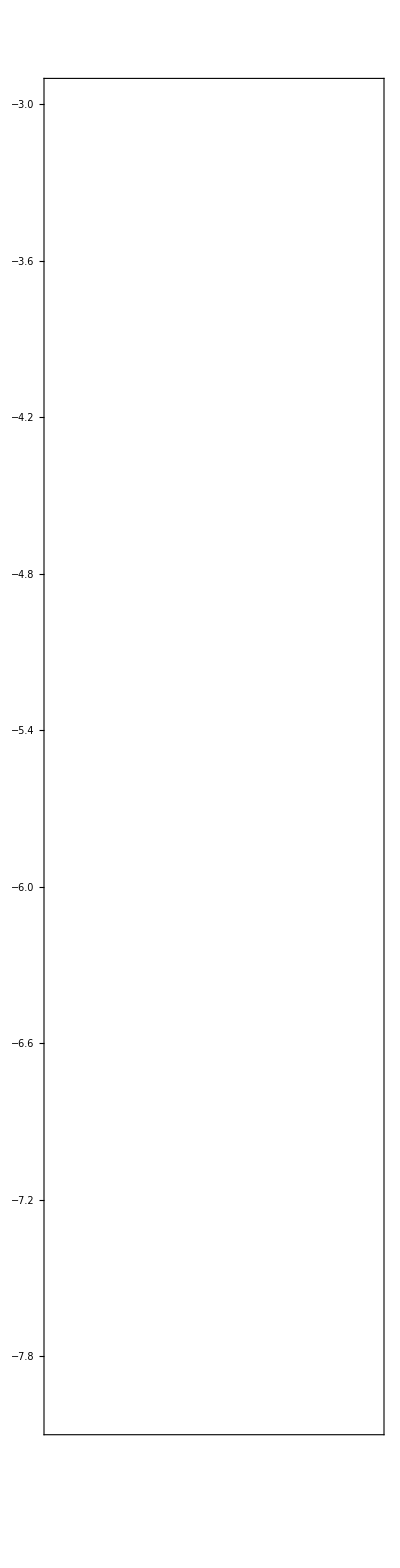
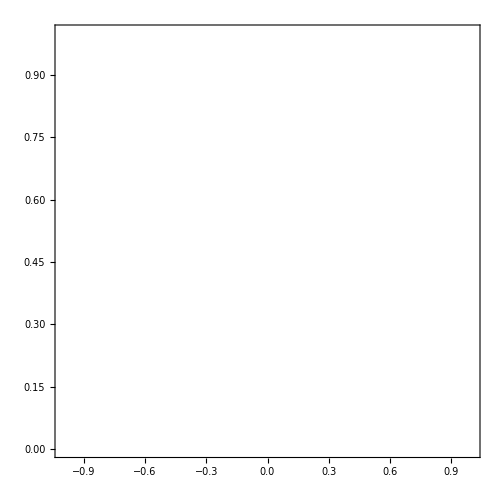
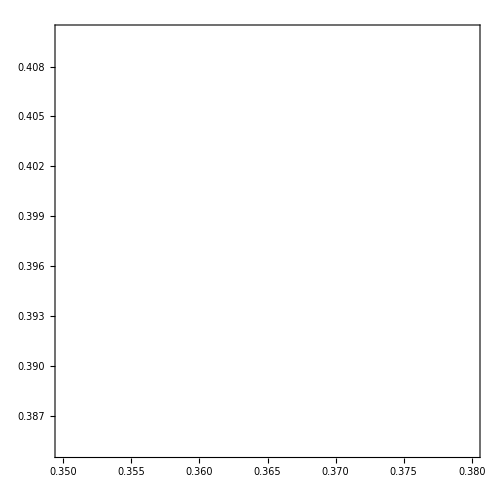
-Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

-Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

-Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

```mathematica
(* FMA results *)
(* As one can see from FMA plots, darker regions correspond to resonace and chaotic initial conditions *)
(* Effect of large FMA index for resonace initial conditions was discussed in previous example *)
(* For the 2nd case, where sample length was doubled, resonance regions are partially averaged out *)
(* The 3d case is the most accurate, but computationaly expensive *)
(* Normally it is more or less safe to use 10^3-10^5 iterations without window shift *)
(* If results seem suspicious further refinement can be performed *)
FMA1
FMA2
FMA3
```

```mathematica
(* Improve FMA plot resolution in frequency space *)
(* Since initial conditions are defined in space of coordinates, e.g. uniform grid as in this example, resolution in frequency space might be poor *)
(* To improve FMA plot resolution in frequency space one can try to generate initial conditions near points that correspond to a less dense region in frequency space (or in some region of interest) *)
(* The following procedure thus can be performed: *)
(* 1) Select points in frequency space (points in some region, close to some resonance or several resonances, points within some interval of FMA index value) *)
(* 2) Find corresponding points in coordinate space and perturb them randomly one or several times *)
(* 3) Filter perturbed points (e.g. keep only positive vertical coordinates) *)
(* 4) Perform FMA for perturbed points *)
(* 5) Add new data and check the result *)

(* Alternatively, it is possible to use denser uniform grid or non-uniform grids in space of coordinates that is denser near DA boundary *)
```

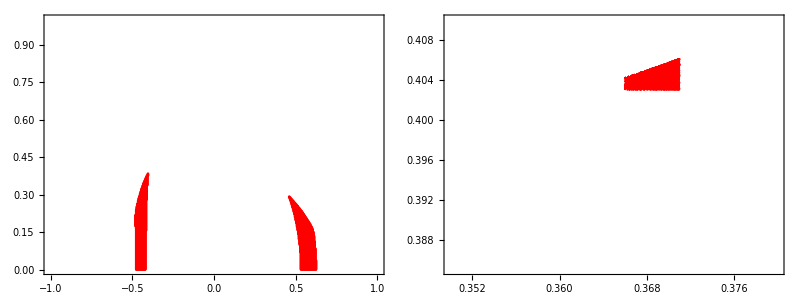

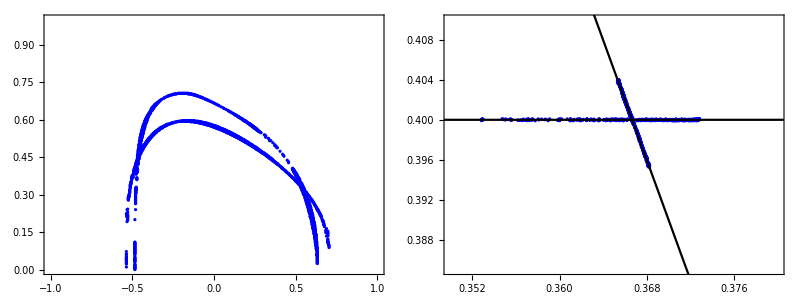

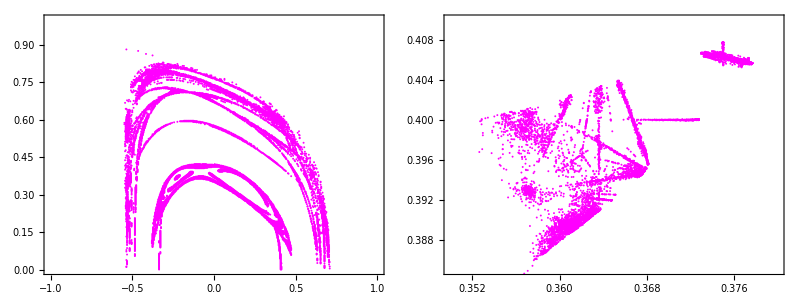

```mathematica
(* As an example, three regions will be used to improve FMA plot resolution in frequency space *) 
(* FMA is performed using Case-1 parameters) *)

(* Region-1: Rectangular region in frequency space *)
(* Select points for given region *)
REG1 = Select[DAT1,Function[And[LessEqual[0.366,Part[Slot[1],3],0.371],LessEqual[0.403,Part[Slot[1],4],0.408]]]] ;
(* Plot selected points *)
Grid[
	List[
		List[
			Show[COR1,ListPlot[Part[REG1,All,List[1,2]],PlotStyle->Red]],
			Show[FRE1,ListPlot[Part[REG1,All,List[3,4]],PlotStyle->Red],Graphics[List[EdgeForm[Black],White,Opacity[0],Rectangle[List[0.366,0.403],List[0.371,0.408]]]]]
		]
	]
]

(* Region-2: Points close to selected resonances *)
(* Using S$RESONANCE$PLOT[] two resonances were selected *)
RES1 = List[0,5,2] ;  (* -- 0*nu_x + 5*nu_y == 2 *)
RES2 = List[6,2,3] ;  (* -- 6*nu_x + 2*nu_y == 3 *)
(* Selection of points close to given resonance can be done witn S$SELECT[] function *) 
SEL1 = S$SELECT[      (* -- select point close to resonance *)
	RES1,             (* -- resonance *)
	5 10^-4,          (* -- distance to resonance in frequncy space *)
	DAT1,             (* -- FMA data *)
	List[3,4]         (* -- positions of frequencies within FMA data *)
] ;
SEL2 = S$SELECT[RES2,5 10^-4,DAT1,List[3,4]] ;
REG2 = Join[SEL1,SEL2] ;
(* Plot selected points *)
Grid[
	List[
		List[
			Show[COR1,ListPlot[Part[REG2,All,List[1,2]],PlotStyle->Blue]],
			Show[
				FRE1,
				ListPlot[Part[REG2,All,List[3,4]],PlotStyle->Blue],
				ContourPlot[{0*X+5*Y==2,6*X+2*Y==3},{X,0.,0.5},{Y,0.,0.5},ContourStyle->Black],
				PlotRange -> List[List[0.350,0.380],List[0.385,0.410]]
			]
		]
	]
]

(* Region-3: Points with large FMA index values *)
REG3 = Select[
	DAT1,
	Function[
		And[
			GreaterEqual[Part[Slot[1],-1],-4.0]
		]
	]
] ;
(* Plot selected points *)
Grid[
	List[
		List[
			Show[COR1,ListPlot[Part[REG3,All,List[1,2]],PlotStyle->Magenta]],
			Show[FRE1,ListPlot[Part[REG3,All,List[3,4]],PlotStyle->Magenta],PlotRange -> List[List[0.350,0.380],List[0.385,0.410]]]
		]
	]
]
```

```mathematica
(* Perturbation of initial conditions in space of coordinates can be done with S$REFINE$INITIALS[] function *)
(* Region-1 *)
(* Select coordinates *)
INI1 = Part[REG1,All,List[1,2]] ;
(* Perturb coordinates *)
INI1 = S$REFINE$INITIALS[  (* -- perturb initials *)
	40,                    (* -- number of repetitions *)
	0.01,                  (* -- perturbation strength  *)
	INI1                   (* -- initials to perturb *)
] ;
(* Filter initials *)
INI1 = DeleteCases[INI1,List[_,_?Negative]] ;
(* Generate full initial condition *)
INI1 = Map[
	Function[
		Block[
			{X,Y},
			{X,Y} = Slot[1] ;
			{1.0,X,10.^-10,Y,10.^-10}
		]
	],
	INI1
] ;
(* Region-2 *)
INI2 = Part[REG2,All,List[1,2]] ;
INI2 = S$REFINE$INITIALS[80,0.02,INI2] ;
INI2 = DeleteCases[INI2,List[_,_?Negative]] ;
INI2 = Map[
	Function[
		Block[
			{X,Y},
			{X,Y} = Slot[1] ;
			{1.0,X,10.^-10,Y,10.^-10}
		]
	],
	INI2
] ;
(* Region-3 *)
INI3 = Part[REG3,All,List[1,2]] ;
INI3 = S$REFINE$INITIALS[20,0.005,INI3] ;
INI3 = DeleteCases[INI3,List[_,_?Negative]] ;
INI3 = Map[
	Function[
		Block[
			{X,Y},
			{X,Y} = Slot[1] ;
			{1.0,X,10.^-10,Y,10.^-10}
		]
	],
	INI3
] ;
INI1//Length
INI2//Length
INI3//Length
```

209772

170958

211867

```mathematica
(* Perform FMA for new initial conditions *)

(* Region-1 *)
INI = INI1 ;
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,1024,8,12,1024,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA,VAL,FRE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2048,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			FRE = Map[Mean,First[FMA]] ;
			VAL = Log10[Plus[$MachineEpsilon,Last[FMA]]] ;
			Flatten[List[Part[POI,List[2,4]],FRE,VAL]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["test_fma_data_1_1.mx",DAT,"MX"]

(* Region-2 *)
INI = INI2 ;
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,1024,8,12,1024,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA,VAL,FRE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2048,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			FRE = Map[Mean,First[FMA]] ;
			VAL = Log10[Plus[$MachineEpsilon,Last[FMA]]] ;
			Flatten[List[Part[POI,List[2,4]],FRE,VAL]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["test_fma_data_1_2.mx",DAT,"MX"]

(* Region-3 *)
INI = INI3 ;
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,1024,8,12,1024,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA,VAL,FRE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2048,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			FRE = Map[Mean,First[FMA]] ;
			VAL = Log10[Plus[$MachineEpsilon,Last[FMA]]] ;
			Flatten[List[Part[POI,List[2,4]],FRE,VAL]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["test_fma_data_1_3.mx",DAT,"MX"]
```

{344.93,Null}

209772

1.

test_fma_data_1_1.mx

{285.122,Null}

168375

0.984891

test_fma_data_1_2.mx

{335.412,Null}

195601

0.923225

test_fma_data_1_3.mx

```mathematica
(* Import saved data *)
DAT0 = Import["test_fma_data_1.mx"] ;
DAT1 = Import["test_fma_data_1_1.mx"] ;
DAT2 = Import["test_fma_data_1_2.mx"] ;
DAT3 = Import["test_fma_data_1_3.mx"] ;
```

```mathematica
(* Check results *)

(* Initial FMA data *)
DAT = Part[DAT0,All,List[3,4,-1]] ;  
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] 

(* Initial FMA data and 1st region *)
DAT = Join[
	Part[DAT0,All,List[3,4,-1]],
	Part[DAT1,All,List[3,4,-1]]
] ;  
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] 

(* Initial FMA data and 2nd region *)
DAT = Join[
	Part[DAT0,All,List[3,4,-1]],
	Part[DAT2,All,List[3,4,-1]]
] ;  
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] 

(* Initial FMA data and 3rd region *)
DAT = Join[
	Part[DAT0,All,List[3,4,-1]],
	Part[DAT3,All,List[3,4,-1]]
] ;  
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] 

(* Initial FMA data and all regions *)
DAT = Join[
	Part[DAT0,All,List[3,4,-1]],
	Part[DAT1,All,List[3,4,-1]],
	Part[DAT2,All,List[3,4,-1]],
	Part[DAT3,All,List[3,4,-1]]
] ;  
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## EXAMPLE-05: FDE

```mathematica
(* Fractal Dimension Estimation *)

(* In this example, basic FDE workflow is presented *)
(* FDE is based on the estimation of fractal dimension from power spectra length computed for different samples *)
(* FDE returns dimension which for regular orbits should be close to one *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* FDE can be computed by S$FDE[] function that uses S$PSL[] function for spectra length computation *) 
(* S$PSL[<SIG>,<OPT>] -- compute power spectra length for input signal <SIG> and option(s) <OPT> *)
S$PSL//Options
(* S$FDE[<RAN>,<SIG>,<OPT>] -- compute FDE for rangle of sample length <RAN> = {<LEN_1>,<LEN_2>,...}, input signal <SIG> and option(s) <OPT> *)
S$FDE//Options
```

{WindowOrder→0,Standardize→True,Level→1.×10^-12,Complex→False}

{WindowOrder→0,Standardize→True,Level→1.×10^-12,Method→Fit,Complex→False}

```mathematica
(* Define quadratic symplectic map with internal aperture (Henon) *)
(* Set map parameters *)
F1 = 2 Pi 0.38 ;
F2 = 2 Pi 0.41 ;
A1 = 0.0 ;
B1 = 1.0 ;
A2 = 0.0 ;
B2 = 1.0 ;
(* Generate compiled map *)
ClearAll[MAP] ;
MAP = With[
	{$Q1 = F1, $Q2 = F2, $W = 1.0, $A1 = A1, $B1 = B1, $A2 = A2, $B2 = B2},
	Compile[
		{{X,_Real,1}},
		Block[
			{W,Q1,P1,Q2,P2},
			{W,Q1,P1,Q2,P2} = X ;
			(* Check aperture and change flag *)
			If[
				Greater[Norm[List[Q1,Q2]],5.0],
				W = 0. ;
			] ;
			(* Iterate for valid flag value *)
			If[
				W > 0.5,
				List[
					W,
					(Cos[$Q1] + $A1 Sin[$Q1])Q1 + ($W(Q1^2-Q2^2)+P1) $B1 Sin[$Q1], 
					(Cos[$Q1] - $A1 Sin[$Q1])($W(Q1^2-Q2^2)+P1) - Q1 (1 + $A1^2)/$B1 Sin[$Q1], 
					(Cos[$Q2] + $A2 Sin[$Q2])Q2 + ($W(-2 Q1 Q2) + P2) $B2 Sin[$Q2], 
					(Cos[$Q2] - $A2 Sin[$Q2])($W(-2 Q1 Q2) + P2) - (1 + $A2^2)/$B2 Q2 Sin[$Q2]
				],
				{W,Q1,P1,Q2,P2}
			]
		],
		CompilationOptions ->  List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
```

```mathematica
(* Compute FDE for several initial conditions *)
(* Generate orbits *)
RES = NestList[MAP,List[1.,0.1106,0.,0.54,0.0],2^20-1] ;              (* -- regular trajectrory close to resonance *)
CHA = NestList[MAP,List[1.,0.6892500005,0.,0.1,0.0],2^20-1] ;         (* -- chaotic trajectory *)
(* Set signals (use 1st coordinate) *)
RES = First[Rest[Transpose[RES]]] ;
CHA = First[Rest[Transpose[CHA]]] ;
(* Compute FDE using samples defined by Range[100000,1000000,100000], i.e. spectra length is computed for 100000, 200000, ..., 1000000 points *)
(* As expected FDE for regular trajectory is close to one, while it is not the fact for chaotic case *)
S$FDE[Range[100000,1000000,100000],RES]//AbsoluteTiming
S$FDE[Range[100000,1000000,100000],CHA]//AbsoluteTiming
```

{0.399554,0.998264}

{0.401692,1.30757}

```mathematica
(* Perform FDE for initial grid in space of coordinates *)
(* Initiallization and intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FDE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[150000,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			DAT = First[Rest[Transpose[DAT]]] ;
			FDE = S$FDE[Range[25000,150000,25000],DAT] ;
			Flatten[List[Part[POI,List[2,4]],FDE]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["test_fde_data_1.mx",DAT,"MX"]
```

501

501

251001

{2459.44,Null}

98655

0.393046

test_fde_data_1.mx

```mathematica
(* Load saved data *)
SetDirectory[NotebookDirectory[]] ;
DAT = Import["test_fde_data_1.mx"] ;
```

```mathematica
(* Use MaTeX for plot labels *)
(* https://github.com/szhorvat/MaTeX/releases *)
<< MaTeX` ;
```

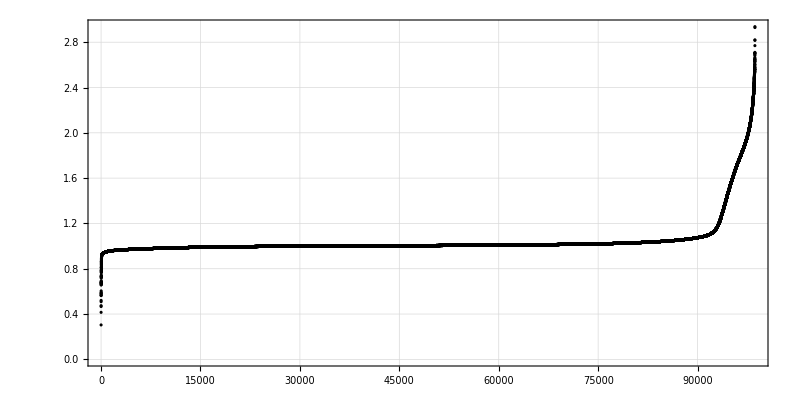

```mathematica
(* Plot sorted FDE values *)
ListPlot[
	Sort[Map[Last,DAT]],
	PlotTheme -> "Detailed",
	ImageSize -> 800,
	AspectRatio -> 1/2,
	PlotStyle -> Black,
	PlotRange -> All
]
```

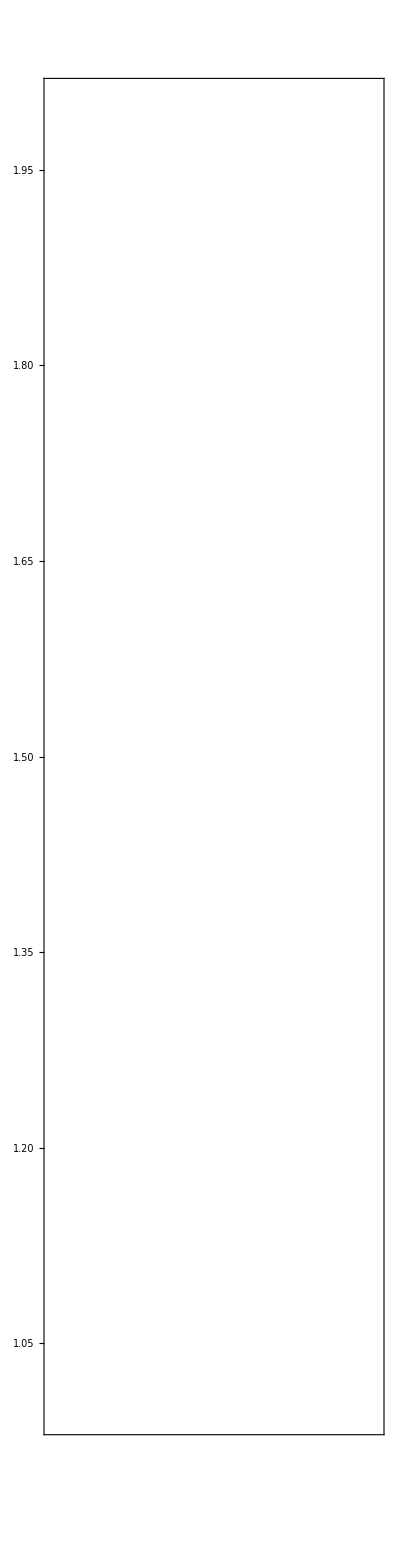
-Graphics--Graphics- | -Graphics--Graphics--Graphics- |

```mathematica
(* Generate FDE color plot *)
(* Set FDE indicator background level *)
LEV = 0. ; 
(* Set FDE indicator interval (values outside this interval are shifted to endpoints) *)       
INT = List[1.,2.] ;
(* Set intervals for coordinates *)
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;
(* Data binarization *)
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
(* Generate color plot and legend *)
COR = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,15] ;
(* Plot result *)
FDE = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\textrm{FDE}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
]
```

## EXAMPLE-06: FLI

```mathematica
(* Fast Lyapunov Indicator *)

(* In this example, basic FLI workflow is presented *)
(* FLI is based on evaluation of tangent vectors *)
(* One or several (orthonormal) deviation vectors can be used for FLI computation *)
(* Maximum number of orthonormal deviation vectors for the given system is equal to its phase space dimension *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* Several functions are available for FLI computation (see recommended reference or SRC_SIGNAL for implementation details) *)

(* <OUT> = S$FLI$ONE[<VEC>] -- compute FLI using one deviation vector *)
(* <VEC>                    -- deviation vector for all iterations, <VEC> = {<VEC_1>,<VEC_2>,...,<VEC_N>} *)
(* <OUT>                    -- list of (folded) FLI indicators *)

(* <OUT> = S$FLI$ALL[<VEC>] -- compute FLI using several deviation vectors *)
(* <VEC>                    -- sequence of deviation vectors for all iterations *)
(* <OUT>                    -- list of (folded) FLI indicators *)

(* <OUT> = S$FLI$LAS[<VEC>] -- compute FLI using several deviation vectors (or S$FLI[<VEC>]) *)
(* <VEC>                    -- sequence of deviation vectors for all iterations *)
(* <OUT>                    -- max FLI indicator *)

(* All FLI functions use S$FLI$FUN function (default is Max) for folding *) 
(* This function removes oscillations of FLI indicator *)
(* {<FLI_1>,<FLI_2>,<FLI_3>,...} => {<FLI_1>,S$FLI$FUN[{<FLI_1>,<FLI_2>}],S$FLI$FUN[{S$FLI$FUN[{<FLI_1>,<FLI_2>}],<FLI_3>}],...} *)
```

```mathematica
(* Define quadratic symplectic map with internal aperture (Henon) with tangent dynamics *)
(* Set map parameters *)
F1 = 2 Pi 0.38 ;
F2 = 2 Pi 0.41 ;
A1 = 0.0 ;
B1 = 1.0 ;
A2 = 0.0 ;
B2 = 1.0 ;
(* Generate compiled map *)
ClearAll[MAP] ;
MAP = With[
	{$Q1 = F1, $Q2 = F2, $W = 1.0, $A1 = A1, $B1 = B1, $A2 = A2, $B2 = B2},
	Compile[
		{{X,_Real,1}},
		Block[
			{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44},
			{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44} = X ;
			(* Check aperture and change flag *)
			If[
				Greater[Norm[List[Q1,Q2]],5.0],
				W = 0. ;
			] ;
			(* Iterate for valid flag value *)
			If[
				W > 0.5,
				(* Map & tangent map *)
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44} = {
					W,
					$B1 (P1 + (Q1^2 - Q2^2) $W) Sin[$Q1] + Q1 (Cos[$Q1] + $A1 Sin[$Q1]),
					-((Q1 (1 + $A1^2) Sin[$Q1])/$B1) + (P1 + (Q1^2 - Q2^2) $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					Q2 Cos[$Q2] + (P2 $B2 + Q2 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					-((Q2 (1 + $A2^2) Sin[$Q2])/$B2) + (P2 - 2 Q1 Q2 $W) (Cos[$Q2] - $A2 Sin[$Q2]),
					V11 Cos[$Q1] + ($B1 (V12 - 2 Q2 V13 $W) + V11 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V11 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V11 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V12 - 2 Q2 V13 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V13 Cos[$Q2] + ($B2 (V14 - 2 Q2 V11 $W) + V13 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					-((V13 (1 + $A2^2) Sin[$Q2])/$B2) + (V14 - 2 (Q2 V11 + Q1 V13) $W) (Cos[$Q2] - $A2 Sin[$Q2]),
					V21 Cos[$Q1] + ($B1 (V22 - 2 Q2 V23 $W) + V21 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V21 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V21 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V22 - 2 Q2 V23 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V23 Cos[$Q2] + ($B2 (V24 - 2 Q2 V21 $W) + V23 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V24 - 2 (Q2 V21 + Q1 V23) $W) Cos[$Q2] - (($A2 $B2 (V24 - 2 Q2 V21 $W) + V23 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2,
					V31 Cos[$Q1] + ($B1 (V32 - 2 Q2 V33 $W) + V31 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V31 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V31 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V32 - 2 Q2 V33 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V33 Cos[$Q2] + ($B2 (V34 - 2 Q2 V31 $W) + V33 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V34 - 2 (Q2 V31 + Q1 V33) $W) Cos[$Q2] - (($A2 $B2 (V34 - 2 Q2 V31 $W) + V33 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2,
					V41 Cos[$Q1] + ($B1 (V42 - 2 Q2 V43 $W) + V41 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V41 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V41 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V42 - 2 Q2 V43 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V43 Cos[$Q2] + ($B2 (V44 - 2 Q2 V41 $W) + V43 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V44 - 2 (Q2 V41 + Q1 V43) $W) Cos[$Q2] - (($A2 $B2 (V44 - 2 Q2 V41 $W) + V43 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2
				} ;
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44},
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44}
			]
		],
		CompilationOptions -> List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
```

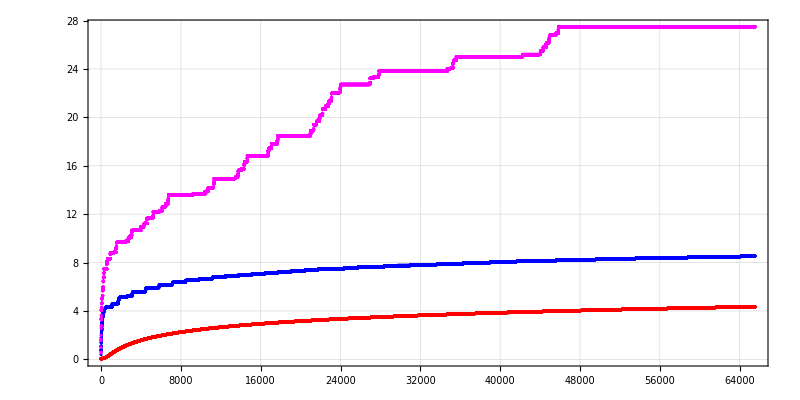

```mathematica
(* Compute FLI indicator (full list) for several initial conditions *)

(* Regular initial condition (red) *)
REG = Flatten[List[List[1.,0.05,0.,0.05,0.],N[IdentityMatrix[4]]]] ;                     (* -- generate initial condition including deviation vectors *)
REG = NestList[MAP,REG,2^16] ;                                                           (* -- iterate map *)
REG = Rest[REG] ;                                                                        (* -- drop initial condition from the list *)
REG = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],REG] ;    (* -- keep only deviation vectors and partition them *)
REG = Transpose[REG] ;                                                                   (* -- form sequence of deviation vectors *)
REG = Apply[S$FLI$ALL,REG] ;                                                             (* -- compute FLI list *)

(* Regular initial condition close to resonance (blue) *)
RES = Flatten[List[List[1.,0.1106,0.,0.54,0.0],N[IdentityMatrix[4]]]] ;
RES = NestList[MAP,RES,2^16] ;
RES = Rest[RES] ;
RES = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],RES] ;
RES = Transpose[RES] ;
RES = Apply[S$FLI$ALL,RES] ;

(* Chaotic initial condition (magenta) *)
CHA = Flatten[List[List[1.,0.6892500005,0.,0.1,0.0],N[IdentityMatrix[4]]]] ;
CHA = NestList[MAP,CHA,2^16] ;
CHA = Rest[CHA] ;
CHA = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],CHA] ;
CHA = Transpose[CHA] ;
CHA = Apply[S$FLI$ALL,CHA] ;

(* Plot result *)
ListPlot[
	List[REG,RES,CHA],
	PlotTheme -> "Detailed",
	ImageSize -> 800,
	AspectRatio -> 1/2,
	PlotStyle -> List[Red, Blue, Magenta]
]
```

```mathematica
(* Perform FLI for initial grid in space of coordinates  *)
(* Initiallization and intitial grid *)
INI = Table[
	Flatten[
		List[
			List[1.0,X,10.^-10,Y,10.^-10],                         (* -- normal initial condition with aperture flag *)
			Orthogonalize[RandomReal[List[-1,+1],List[4,4]]]       (* -- tangent part *)
		]
	],
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FLI},
			POI = Slot[1] ;                            
			DAT = NestList[MAP,POI,Subtract[2^12,1]] ; 
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			DAT = Rest[DAT] ;
			DAT = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],DAT] ;
			DAT = Transpose[DAT] ;
			FLI = Apply[S$FLI$LAS,DAT] ;
			Set[$HistoryLength,0] ;
			Clear[DAT] ;
			Flatten[List[Part[POI,List[2,4]],FLI]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["test_fli_data_1.mx",DAT,"MX"]
```

501

501

251001

{543.68,Null}

102708

0.409194

test_fli_data_1.mx

```mathematica
(* Load saved data *)
SetDirectory[NotebookDirectory[]] ;
DAT = Import["test_fli_data_1.mx"] ;
```

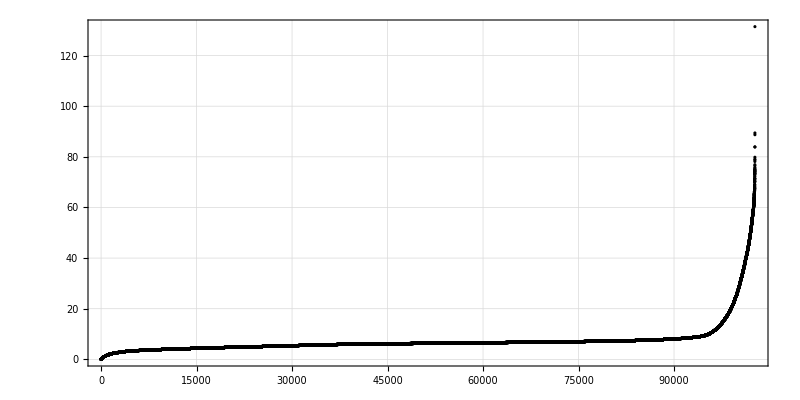

```mathematica
(* Plot sorted FLI values *)
ListPlot[
	Sort[Map[Last,DAT]],
	PlotTheme -> "Detailed",
	ImageSize -> 800,
	AspectRatio -> 1/2,
	PlotStyle -> Black,
	PlotRange -> All
]
```

```mathematica
(* Use MaTeX for plot labels *)
(* https://github.com/szhorvat/MaTeX/releases *)
<< MaTeX` ;
```

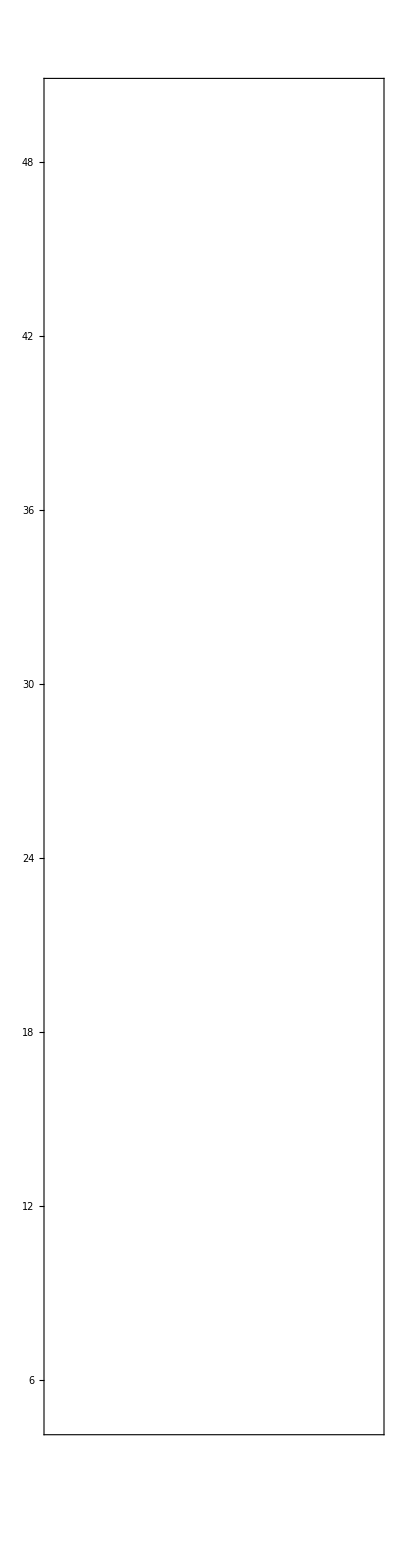
-Graphics--Graphics- | -Graphics--Graphics--Graphics-

```mathematica
(* Generate FLI color plot *)
(* Interval is selected based on the above plot *)
(* As it can be seen chaotic initial conditions mostly appear near the boundary of stability *)
(* Some resonance structure can still be seen for regular regions *)
(* Set FLI background level *)
LEV = 0. ;                    
(* Set FLI interval *) 
INT = List[5.,50.] ;
(* Set intervals for coordinates *)
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;
(* Data binarization *)
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
(* Generate color plot and legend *)
COR = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,15] ;
(* Show result *)
FLI = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{FLI}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
]
```

## EXAMPLE-07: SALI & GALI

```mathematica
(* The Smaller and the Generalized Alignment Indices *)

(* In this example, basic SALI & GALI workflow is presented *)
(* SALI & GALI are based on evaluation of (normalized at each iteration) tangent vectors *)
(* Two deviation (orthonormal) vectors can be used for SALI computation *)
(* Two or more deviation (orthonormal) vectors can be used for GALI computation *)
(* Maximum number of orthonormal deviation vectors for the given system is equal to its phase space dimension *)
(* SALI is equivalent to GALI(2), i.e. GALI computed using two deviation vectors *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* SALI indicator can be computed using  S$SALI[] function *)
(* <OUT> = S$SALI[{<VEC_1>,<VEC_2>}] *)
(* <VEC_I> -- deviation vector given at some iteration *)
(* <OUT> -- SALI indicator value *)

(* GALI indicator(s) can be computed using  S$GALI[] function *)
(* <OUT> = S$GALI[{<VEC_1>,<VEC_2>,...}] *)
(* <VEC_I> -- deviation vector given at some iteration *)
(* <OUT> -- GALI indicator value *)
(* GALI(2) = S$GALI[{<VEC_1>,<VEC_2>}] *)
(* GALI(3) = S$GALI[{<VEC_1>,<VEC_2>,<VEC_3>}] *)

(* Both S$SALI[] and S$GALI[] functions use S$INDEX$LEVEL parameter (some small number) which is added to actual indicator value *)
(* Default level value is: *)
S$INDEX$LEVEL
```

1.×10^-14

```mathematica
(* Define quadratic symplectic map with internal aperture (Henon) with normalized tangent dynamics *)
(* Set map parameters *)
F1 = 2 Pi 0.38 ;
F2 = 2 Pi 0.41 ;
A1 = 0.0 ;
B1 = 1.0 ;
A2 = 0.0 ;
B2 = 1.0 ;
(* Generate compiled map *)
ClearAll[MAP] ;
MAP = With[
	{$Q1 = F1, $Q2 = F2, $W = 1.0, $A1 = A1, $B1 = B1, $A2 = A2, $B2 = B2},
	Compile[
		{{X,_Real,1}},
		Block[
			{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44},
			{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44} = X ;
			(* Check aperture and change flag *)
			If[
				Greater[Norm[List[Q1,Q2]],5.0],
				W = 0. ;
			] ;
			(* Iterate for valid flag value *)
			If[
				W > 0.5,
				(* Map & tangent map *)
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44} = {
					W,
					$B1 (P1 + (Q1^2 - Q2^2) $W) Sin[$Q1] + Q1 (Cos[$Q1] + $A1 Sin[$Q1]),
					-((Q1 (1 + $A1^2) Sin[$Q1])/$B1) + (P1 + (Q1^2 - Q2^2) $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					Q2 Cos[$Q2] + (P2 $B2 + Q2 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					-((Q2 (1 + $A2^2) Sin[$Q2])/$B2) + (P2 - 2 Q1 Q2 $W) (Cos[$Q2] - $A2 Sin[$Q2]),
					V11 Cos[$Q1] + ($B1 (V12 - 2 Q2 V13 $W) + V11 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V11 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V11 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V12 - 2 Q2 V13 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V13 Cos[$Q2] + ($B2 (V14 - 2 Q2 V11 $W) + V13 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					-((V13 (1 + $A2^2) Sin[$Q2])/$B2) + (V14 - 2 (Q2 V11 + Q1 V13) $W) (Cos[$Q2] - $A2 Sin[$Q2]),
					V21 Cos[$Q1] + ($B1 (V22 - 2 Q2 V23 $W) + V21 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V21 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V21 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V22 - 2 Q2 V23 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V23 Cos[$Q2] + ($B2 (V24 - 2 Q2 V21 $W) + V23 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V24 - 2 (Q2 V21 + Q1 V23) $W) Cos[$Q2] - (($A2 $B2 (V24 - 2 Q2 V21 $W) + V23 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2,
					V31 Cos[$Q1] + ($B1 (V32 - 2 Q2 V33 $W) + V31 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V31 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V31 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V32 - 2 Q2 V33 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V33 Cos[$Q2] + ($B2 (V34 - 2 Q2 V31 $W) + V33 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V34 - 2 (Q2 V31 + Q1 V33) $W) Cos[$Q2] - (($A2 $B2 (V34 - 2 Q2 V31 $W) + V33 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2,
					V41 Cos[$Q1] + ($B1 (V42 - 2 Q2 V43 $W) + V41 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V41 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V41 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V42 - 2 Q2 V43 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V43 Cos[$Q2] + ($B2 (V44 - 2 Q2 V41 $W) + V43 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V44 - 2 (Q2 V41 + Q1 V43) $W) Cos[$Q2] - (($A2 $B2 (V44 - 2 Q2 V41 $W) + V43 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2
				} ;
				(* Normalization of deviation vectors *)
				{V11,V12,V13,V14} = {V11,V12,V13,V14}/Norm[{V11,V12,V13,V14}] ; 
				{V21,V22,V23,V24} = {V21,V22,V23,V24}/Norm[{V21,V22,V23,V24}] ; 
				{V31,V32,V33,V34} = {V31,V32,V33,V34}/Norm[{V31,V32,V33,V34}] ; 
				{V41,V42,V43,V44} = {V41,V42,V43,V44}/Norm[{V41,V42,V43,V44}] ; 
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44},
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44}
			]
		],
		CompilationOptions -> List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
```

```mathematica
(* Perform SALI & GALI for initial grid in space of coordinates *)
(* In this example SALI and GALI(2/3/4) are computed *)
(* MAP is iterated 2^10 times, then additional 2^8 iterations are performed and orbit history is recorded *)
(* For all recorded orbits SALI & GALI indicators are computed and minimum values are returned *)
(* Initiallization and intitial grid *)
INI = Table[
	Flatten[
		List[
			List[1.0,X,10.^-10,Y,10.^-10],                         (* -- normal initial condition with aperture flag *)
			Orthogonalize[RandomReal[List[-1,+1],List[4,4]]]       (* -- tangent part *)
		]
	],
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,DV1,DV2,DV3,DV4,SAL,GAL},
			POI = Slot[1] ;                            
			DAT = Nest[MAP,POI,Subtract[2^10,1]] ; 
			If[SameQ[Chop[First[DAT]],0],Throw[Nothing]] ;
			DAT = NestList[MAP,DAT,Subtract[2^8,1]] ; 
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			DAT = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],DAT] ;
			List[DV1,DV2,DV3,DV4] = Transpose[DAT] ;
			SAL = Min[Map[S$SALI,Transpose[List[DV1,DV3]]]] ;
			GAL = List[
				Min[Map[S$GALI,Transpose[List[DV1,DV3]]]],
				Min[Map[S$GALI,Transpose[List[DV1,DV2,DV3]]]],
				Min[Map[S$GALI,Transpose[List[DV1,DV2,DV3,DV4]]]]
			] ;
			Flatten[List[Part[POI,List[2,4]],SAL,GAL]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save data *)
SetDirectory[NotebookDirectory[]] ;
Export["test_ali_data_1.mx",DAT,"MX"]
```

501

501

251001

```mathematica
(* In this example T-GALI(MAX) is computed (compute 'time' required to reach given index level using all deviation vectors) *)
(* MAP is iterated up to 2^18 times *)
(* After each iteration apetrure is checked and GALI(4) is computed *)
(* If its value is less then 10^-10, the iteration loop is terminated and  number of iterations is returned *)
(* Initiallization and intitial grid *)
INI = Table[
	Flatten[
		List[
			List[1.0,X,10.^-10,Y,10.^-10],                         (* -- normal initial condition with aperture flag *)
			Orthogonalize[RandomReal[List[-1,+1],List[4,4]]]       (* -- tangent part *)
		]
	],
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,ITR,DAT,GAL},
			POI = Slot[1] ;
			(* Iteration loop *)                            
			Do[
				List[
					POI = MAP[POI] ;
					If[SameQ[Chop[First[POI]],0],Throw[Nothing]] ;
					DAT = Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]][POI] ;
					DAT = Transpose[DAT] ;
					GAL = S$GALI[DAT] ;
					If[
						LessEqual[GAL,N[Log10[Power[10,Times[Subtract[0,1],10]]]]],
						Throw[Flatten[List[Part[Slot[1],List[2,4]],N[ITR]]]] ;
					] ;
				],
				List[ITR,1,2^18]
			] ;
			(* Value is larger then given level for max number of iterations *)
			Flatten[List[Part[Slot[1],List[2,4]],N[2^18]]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; // AbsoluteTiming
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save data *)
SetDirectory[NotebookDirectory[]] ;
Export["test_ali_data_2.mx",DAT,"MX"]
```

501

501

251001

{7433.39,Null}

141725

0.564639

test_ali_data_2.mx

```mathematica
(* Load saved data *)
SetDirectory[NotebookDirectory[]] ;
DAT1 = Import["test_ali_data_1.mx"] ; 
DAT2 = Import["test_ali_data_2.mx"] ;
```

```mathematica
(* Use MaTeX for plot labels *)
(* https://github.com/szhorvat/MaTeX/releases *)
<< MaTeX` ;
```

```mathematica
(* Generate color plots *)

(* SALI *)
DAT = Part[DAT1,All,List[1,2,3]] ;
LEV = 0. ;                     
INT = List[-10.,-2.] ;
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;          
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT$COLOR = "SunsetColors" ;
COR = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,15] ;
SALI = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{SALI}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;

(* GALI(2) *)
DAT = Part[DAT1,All,List[1,2,4]] ;
LEV = 0. ;                     
INT = List[-10.,-2.] ;
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;          
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT$COLOR = "SunsetColors" ;
COR = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,15] ;
GALI2 = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{GALI(2)}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;

(* GALI(3) *)
DAT = Part[DAT1,All,List[1,2,5]] ;
LEV = 0. ;                     
INT = List[-10.,-2.] ;
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;          
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT$COLOR = "SunsetColors" ;
COR = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,15] ;
GALI3 = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{GALI(3)}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;

(* GALI(4) *)
DAT = Part[DAT1,All,List[1,2,6]] ;
LEV = 0. ;                     
INT = List[-10.,-2.] ;
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;          
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT$COLOR = "SunsetColors" ;
COR = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,15] ;
GALI4 = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{GALI(4)}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;

(* T-GALI(MAX) *)
DAT = Part[DAT2,All,List[1,2,3]] ;
DAT = MapAt[Log10,DAT,List[All,-1]] ;
LEV = 0. ;                     
INT = Log10[List[2^10,2.^18]] ;
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;          
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
S$COLOR$PLOT$COLOR = "SunsetColors" ;
COR = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,15] ;
TGALI = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{T-GALI(MAX)}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;
```

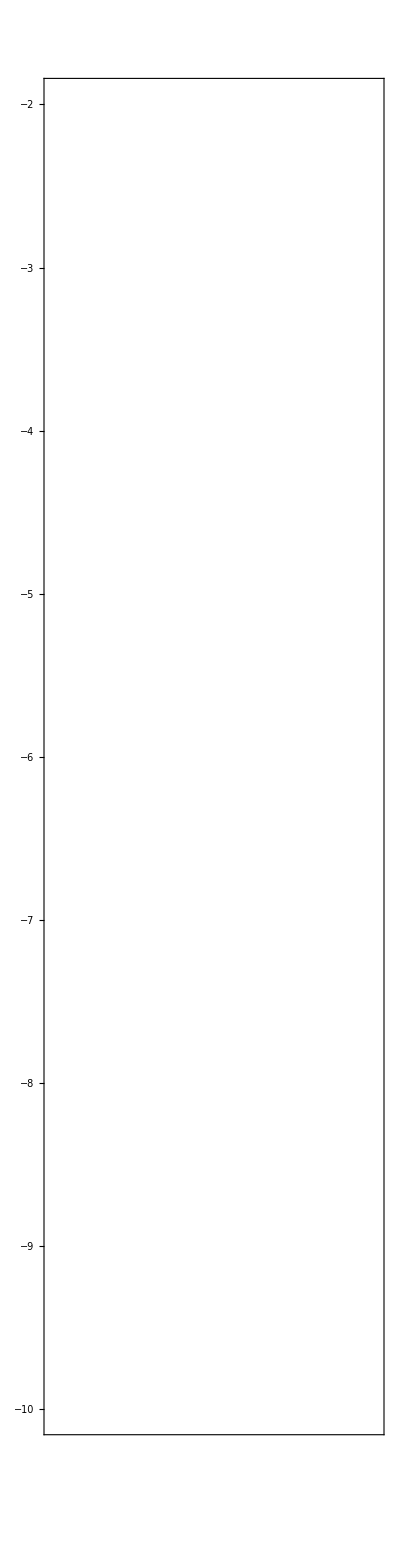
-Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics--Graphics-

-Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics--Graphics-

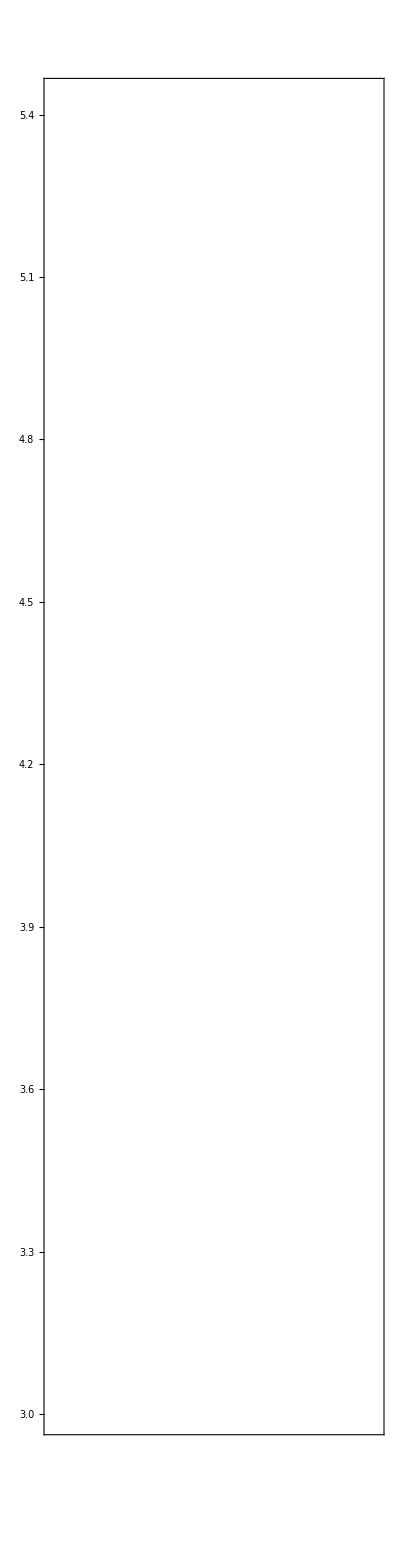
-Graphics--Graphics- | -Graphics--Graphics--Graphics-

```mathematica
(* Show results *)
(* For SALI & GALI range of indicators was chosen to be [-10,-1], for T-GALI(MAX)  range of indicators was chosen to be [log10 2^10,log10 2^18] *)
(* SALI and GALI(2) *)
Grid[List[List[SALI,GALI2]]]
(* GALI(3) and GALI(4) *)
Grid[List[List[GALI3,GALI4]]]
(* T-GALI(MAX) *)
TGALI
```

## EXAMPLE-08: FREQUENCY.F90

```mathematica
(* File frequency.f90 contains simplified FORTRAN implementation of S$FREQUENCY[] function *)
(* Input signal (real or complex) should have power of two length *)
(* Parameters should be modified in FREQUENCY.F90 file *)
(* NUM -- signal length (integer) *)
(* FLA -- complex flag (integer), FLA=1(2) should be used for complex(real) input signal) *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
Get["CompiledFunctionTools`"] 
Get["CCompilerDriver`"]
```

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,2,2048,8,12,1024,Automatic] ;
```

```mathematica
(* Define test signal and estimate frequency *)
FRE = 0.123456789 ;
SIG = 0.1 + Sin[2 Pi FRE Range[S$WINDOW$LENGTH]] ;
REF = First[S$FREQUENCY[SIG]]
FRE - REF
```

0.123457

3.46945×10^-16

```mathematica
(* Generate and run external program *)
(* Parameters <NUM> = 2048 and <FLA> = 2 should be changed in frequency.f90 file *)
(* Set directory *)
SetDirectory[NotebookDirectory[]] ;
(* Program *)
PRO = "
PROGRAM EXAMPLE
  USE FREQUENCY, ONLY: SEARCH
  IMPLICIT NONE
  INTEGER,PARAMETER :: RK=SELECTED_REAL_KIND(15,307)
  INTEGER,PARAMETER :: NUM = 2048
  REAL(RK),PARAMETER :: PI=3.141592653589793238460_RK
  REAL(RK),PARAMETER :: TWO_PI=2.0_RK*PI
  COMPLEX(RK),DIMENSION(NUM) :: ARR
  INTEGER :: I
  DO I=1,NUM,1
    ARR(I)=SIN(2._RK*PI*0.123456789_RK*REAL(I,RK))
  END DO
  ARR=ARR+0.1_RK
  WRITE(*,*) SEARCH(2,ARR)
END PROGRAM EXAMPLE
" ;
(* Export program *)
Export["example.f90",PRO,"String"] ;
(* Compile *)
Run["gfortran -o frequency -O3 -ffast-math -march=native frequency.f90 example.f90"] ;
(* Run *)
RES = RunProcess["./frequency","StandardOutput"] ;
RES = First[ImportString[RES,"List"]]
(* Check result *)
FRE-RES
```

0.123457

2.27596×10^-15

```mathematica
(* Generate library (frequency computation) *)
(* Parameters <NUM> = 2048 and <FLA> = 2 should be changed in frequency.f90 file *)
(* Wrapper *)
(* Set directory *)
SetDirectory[NotebookDirectory[]] ;
WRA = "
#include \"WolframLibrary.h\"
#include \"WolframCompileLibrary.h\" 
DLLEXPORT mint WolframLibrary_getVersion(){
	return WolframLibraryVersion ;
}
DLLEXPORT int WolframLibrary_initialize(WolframLibraryData libData){
	return 0 ;
}			
extern \"C\" {
	mreal task_(mcomplex a[]) ;
} 	
EXTERN_C DLLEXPORT int task(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res){
	MTensor signal ;
	double frequency ; 
	signal = MArgument_getMTensor(Args[0]) ;
	frequency = task_(MTensor_getComplexDataMacro(signal)) ;
	MArgument_setReal(Res,frequency) ;
	return LIBRARY_NO_ERROR ;
}
" ;
(* Export wrapper *)
Export["wrapper.cc",WRA,"String"] ;
(* Program *)
PRO = "
FUNCTION TASK(SIGNAL)
	USE FREQUENCY, ONLY: SEARCH
	IMPLICIT NONE
	INTEGER,PARAMETER :: RK=SELECTED_REAL_KIND(15,307)
	INTEGER,PARAMETER :: NUM = 2048
    REAL(RK),PARAMETER :: PI=3.141592653589793238460_RK
    REAL(RK),PARAMETER :: TWO_PI=2.0_RK*PI
	REAL(RK) :: TASK
	COMPLEX(RK), DIMENSION(2048) :: SIGNAL
	TASK = SEARCH(2,SIGNAL)
	RETURN
END FUNCTION TASK
" ;
Export["task.f90",PRO,"String"] ;
(* Create library *)
Run["gfortran -c -O3 -ffast-math -march=native frequency.f90 task.f90"] ;
CreateLibrary[
	{"wrapper.cc","frequency.o","task.o"},
	"task",
	Rule["TargetDirectory",NotebookDirectory[]],
	Rule["CleanIntermediate",True],
	Rule["CompileOptions","-O3 -ffast-math -march=native"],
	Rule["Debug",False]
] ;
(* Load libray *)
ClearAll[LIB] ;
LIB = LibraryFunctionLoad[StringJoin[NotebookDirectory[],"task"],"task",List[List[Complex,1]],Real] ;
(* Test library *)
RES = LIB[SIG]
FRE - RES
(* Unload library *)
LibraryFunctionUnload[LIB]
```

0.123457

2.27596×10^-15

```mathematica
(* Generate library (FMA computation) *)
(* Parameters <NUM> = 2048 and <FLA> = 1 should be changed in frequency.f90 file *)
(* Wrapper *)
(* Set directory *)
SetDirectory[NotebookDirectory[]] ;
WRA = "
#include \"WolframLibrary.h\"
#include \"WolframCompileLibrary.h\" 
DLLEXPORT mint WolframLibrary_getVersion(){
	return WolframLibraryVersion ;
}
DLLEXPORT int WolframLibrary_initialize(WolframLibraryData libData){
	return 0 ;
}			
extern \"C\" {
	void fma_(mreal a[]) ;
} 		
EXTERN_C DLLEXPORT int fma(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res){
	MTensor A ;
	A = MArgument_getMTensor(Args[0]) ;
    fma_(MTensor_getRealDataMacro(A)) ;
    MArgument_setMTensor(Res,A) ;
	return LIBRARY_NO_ERROR ;
}
" ;
(* Export wrapper *)
Export["wrapper.cc",WRA,"String"] ;
(* Program *)
PRO = "
SUBROUTINE FMA(DATA)
	USE FREQUENCY, ONLY: SEARCH
	IMPLICIT NONE
	INTEGER,PARAMETER :: RK=SELECTED_REAL_KIND(15,307)
	INTEGER,PARAMETER :: NUM = 2048
    REAL(RK),PARAMETER :: PI=3.141592653589793238460_RK
    REAL(RK),PARAMETER :: TWO_PI=2.0_RK*PI
	REAL(RK), DIMENSION(5), INTENT(INOUT) :: DATA
	REAL(RK), DIMENSION(2) :: INITIAL
	REAL(RK), DIMENSION(2*NUM) :: Q1, P1, Q2, P2
	REAL(RK), PARAMETER :: F1 = TWO_PI*0.38_RK
	REAL(RK), PARAMETER :: F2 = TWO_PI*0.41_RK
	REAL(RK), PARAMETER :: COS1 = COS(F1)
	REAL(RK), PARAMETER :: SIN1 = SIN(F1)
	REAL(RK), PARAMETER :: COS2 = COS(F2)
	REAL(RK), PARAMETER :: SIN2 = SIN(F2)
	INTEGER :: I
	REAL(RK), DIMENSION(4) :: FRE
	COMPLEX(RK), DIMENSION(NUM) :: SIGNAL

	Q1(1) = DATA(1)
	P1(1) = 1.0E-10_RK
	Q2(1) = DATA(2)
	P2(1) = 1.0E-10_RK
	
	DO I=1,4096-1,1
		IF((Q1(I)*Q1(I)+Q2(I)*Q2(I)).GE.25.0_RK)THEN
			DATA(1) = Q1(1)
			DATA(2) = Q2(1)
			DATA(3) = 0.0_RK
			DATA(4) = 0.0_RK
			DATA(5) = 0.0_RK
			RETURN
		ENDIF
		Q1(I+1) = Q1(I)*COS1+(P1(I)+Q1(I)*Q1(I)-Q2(I)*Q2(I))*SIN1
		P1(I+1) = (P1(I)+Q1(I)*Q1(I)-Q2(I)*Q2(I))*COS1-Q1(I)*SIN1
		Q2(I+1) = Q2(I)*COS2+(P2(I)-2.0_RK*Q1(I)*Q2(I))*SIN2
		P2(I+1) = (P2(I)-2.0_RK*Q1(I)*Q2(I))*COS2 - Q2(I)*SIN2
	END DO

	IF((Q1(4096)*Q1(4096)+Q2(4096)*Q2(4096)).GE.25.0_RK)THEN
		DATA(1) = Q1(1)
		DATA(2) = Q2(1)
		DATA(3) = 0.0_RK
		DATA(4) = 0.0_RK
		DATA(5) = 0.0_RK
		RETURN
	ENDIF
	
	SIGNAL = CMPLX(Q1(1:NUM:1),P1(1:NUM:1),RK)
	FRE(1) = SEARCH(2,SIGNAL)
	SIGNAL = CMPLX(Q1(NUM+1:2*NUM:1),P1(NUM+1:2*NUM:1),RK)
    FRE(2) = SEARCH(2,SIGNAL)
	SIGNAL = CMPLX(Q2(1:NUM:1),P2(1:NUM:1),RK)
	FRE(3) = SEARCH(2,SIGNAL)
	SIGNAL = CMPLX(Q2(NUM+1:2*NUM:1),P2(NUM+1:2*NUM:1),RK)
    FRE(4) = SEARCH(2,SIGNAL)

	DATA(1) = Q1(1)
	DATA(2) = Q2(1)
	DATA(3) = 0.5_RK*(FRE(1)+FRE(2))
	DATA(4) = 0.5_RK*(FRE(3)+FRE(4))
	DATA(5) = LOG10(SQRT((FRE(1)-FRE(2))**2 + (FRE(3)-FRE(4))**2)+1.E-16_RK)
END SUBROUTINE FMA
" ;
Export["fma.f90",PRO,"String"] ;
(* Create library *)
Run["gfortran -c  -O3 -ffast-math -march=native frequency.f90 fma.f90 "] ; 
CreateLibrary[
	{"wrapper.cc","frequency.o","fma.o"},
	"fma",
	Rule["TargetDirectory",NotebookDirectory[]],
	Rule["CleanIntermediate",True],
	Rule["CompileOptions","-O3 -ffast-math -march=native"],
	Rule["Debug",False]
] ;
(* Load libray *)
ClearAll[LIB] ;
LIB = LibraryFunctionLoad[StringJoin[NotebookDirectory[],"fma"],"fma",List[List[Real,1]],List[Real,1]] ;
(* Safety first *)
ClearAll[FUN] ;
FUN[VAR_] := LIB[VAR] /; Apply[And,Map[NumberQ,VAR]] ;
(* Test *)
FUN[{10.^-10,10.^-10,0.,0.,0.}]
LibraryFunctionUnload[LIB]
```

{1.×10^-10,1.×10^-10,0.38,0.41,-14.6449}

```mathematica
(* Perfom FMA (compare with 2nd case in FMA example, run time was about 300s) *)
(* Intitial grid *)
INI = Table[
	{X,Y,0.,0.,0.},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,2048,8,12,1024,Automatic] ;
(* Run *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
OUT = ParallelMap[FUN,INI] ; // AbsoluteTiming
OUT = DeleteCases[OUT,List[_,_,0.,0.,0.]] ;
OUT = Developer`ToPackedArray[OUT] ;
Length[OUT]
N[Divide[Length[OUT],Length[INI]]]
```

501

501

251001

{60.2484,Null}

102676

0.409066

```mathematica
(* Plot results *)
<< MaTeX` ;

DAT = Part[OUT,All,List[1,2,-1]] ;  
LEV = 0. ;                     
INT = List[-8.,-3.] ;          
HOR = List[-1.0,1.0] ;         
VER = List[0.0,1.0] ;          
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
COR = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,15] ;

DAT = Part[OUT,All,List[3,4,-1]] ;  
LEV = 0. ;           
INT = List[-8.,-3.] ;
HOR = List[0.350,0.380] ;
VER = List[0.385,0.410] ; 
BIN = S$BINARIZE$REGION[500,500,HOR,VER,DAT,Rule["Level",LEV]] ;
FRE = S$COLOR$PLOT[LEV,INT,HOR,VER,BIN,Rule[ImageSize,500],Rule[AspectRatio,1]] ;

FMA = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
]
```

-Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

```mathematica
(* 2nd case FMA result *)
```

-Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

## EXAMPLE-09: Frequency correction

```mathematica
(* In this example frequency correction is performed based on: *)
(* J. Laskar, Frequency map analysis and quasiperiodic decompositions, 2003 *)
(* https://arxiv.org/abs/math/0305364 *)

(* From theorem 1 & 2 of the above reference, it follows that ones quasiperiodic decomposition is performed one can find corrections for frequencies *)
(* In fact, there is no need to use the result of these theorems directly *)
(* One can proceed as follows: *)
(* 1) Perform quasiperiodic decomposition for the given signal <sig> and obtain corresponding approximation <sig1> together with frequencies <fre1> *)
(* 2) For <sig2> perform another quasiperiodic decomposition and its corresponding approximation is <sig3> and frequencies <fre2> *)
(* 3) Corrected frequencies are <fre3> = 2 <fre1> - <fre2> *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* Define test signal *)
FRE = 0.123456 ;
LEN = 128 ;
SIG = 0.5 Cos[2 Pi FRE Range[LEN]] + 0.01 Cos[2 Pi 2 FRE Range[LEN]] + 0.005 Cos[2 Pi 3 FRE Range[LEN]] ;
```

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,2,LEN,8,12,LEN,Automatic] ;
```

```mathematica
(* Set data for 1st decomposition *)
DAT = SIG ;
(* 1st decomposition *)
RS1 = S$QUASIPERIODIC$SUBTRACT[3,LinearModelFit,SIG] ;
FR1 = RS1["Frequencies"] ;
(* Set data for 2nd decomposition *)
DAT = RS1["Function"][Range[LEN]] ;
(* 2nd decomposition *)
RS2 = S$QUASIPERIODIC$SUBTRACT[3,LinearModelFit,DAT] ;
FR2 = RS2["Frequencies"] ;
(* Corrected frequencies *)
FR3 = Subtract[Times[2,FR1],FR2] ;
(* Check result *)
Subtract[FR1,Times[FRE,Range[3]]]
Subtract[FR3,Times[FRE,Range[3]]]

Last[S$FIT$MODEL[FR1,SIG]]["BestFitParameters"]
Last[S$FIT$MODEL[FR3,SIG]]["BestFitParameters"]
```

{5.76262×10^-10,-1.67208×10^-8,8.99312×10^-10}

{-2.69229×10^-15,5.27911×10^-14,2.66454×10^-15}

{-1.67391×10^-9,0.5,0.01,0.005,1.17314×10^-7,-6.80804×10^-8,1.82449×10^-9}

{7.91103×10^-15,0.5,0.01,0.005,-5.45804×10^-13,2.15608×10^-13,6.01559×10^-15}